# Ejecución del Monte-Carlo Simplificado pa la tesis

```mathematica
Needs["Quantum`"]
Needs["MaTeX`"]
Get["/media/storage/ciencia/investigacion/tesis/CoolTools2.m"]
Get["/media/storage/ciencia/investigacion/tesis/codigos-tesis/usefulFunctions.wl"]
```

```mathematica
SetDirectory["/media/storage/ciencia/investigacion/tesis/muestras_MCS"]
```

/media/storage/ciencia/investigacion/tesis/muestras_MCS

## Ejecución preliminar del algoritmo

```mathematica
minimizationStep[{initialstate_, targetstate_ , p_}, δ_?((0<#<1)&), τ_?((0<#<1)&)]:=
With[{U = randomSmallEvolution[4, δ]},
	With[{newstate = Chop[U.initialstate.ConjugateTranspose[U]]},
	If[Norm[targetstate-coarseGraining2[newstate,p], "Frobenius"]<Norm[targetstate-coarseGraining2[initialstate,p],"Frobenius"],
	    newstate,
		RandomChoice[{τ, 1 - τ}->{newstate,initialstate}]]]];
```

```mathematica
(*initialstate es una matriz de 4x4 y targetstate es de 2x2*)
(*Esta función no devuelve un muestra completa, sino sólo un estado perteneciente a la preimagen*)
simpleMCMinimization[{initialstate_,targetstate_,p_}, ϵ_?((0<#<1)&), δ_?((0<#<1)&), τ_?((0<#<1)&)]:=
Module[{maxlimit = 3000},
		NestWhile[minimizationStep[{#,targetstate, p}, δ, τ]&,
				 initialstate,
				 (Norm[targetstate - coarseGraining2[#,p], "Frobenius"] > ϵ)&, 1, maxlimit]]
```

```mathematica
simpleMCMinimizationList[{initialstate_,targetstate_,p_}, ϵ_?((0<#<1)&), δ_?((0<#<1)&), τ_?((0<#<1)&)]:=
Module[{maxlimit = 3000},
		NestWhileList[minimizationStep[{#,targetstate, p}, δ, τ]&,
				 initialstate,
				 (Norm[targetstate - coarseGraining2[#,p], "Frobenius"] > ϵ)&, 1, maxlimit]]
```

```mathematica
simpleMonteCarloSample[size_, targetstate_, p_, ϵ_, δ_, τ_]:=
		simpleMCMinimization[{#, targetstate, p}, ϵ, δ, τ]& /@ ketsToDensity[randomKets[4, size]];
```

```mathematica
simpleMonteCarloSampleList[size_, targetstate_, p_, ϵ_, δ_, τ_]:=
		simpleMCMinimizationList[{#, targetstate, p}, ϵ, δ, τ]& /@ ketsToDensity[randomKets[4, size]];
```

```mathematica
(*Parámetros cuánticos*)
rz = 0.5;
swapP = 0.8;
target = (IdentityMatrix[2] + rz PauliMatrix[3])/2;
target//MatrixForm
```

(0.75 | 0.
0. | 0.25)

```mathematica
(*Parámetros del algoritmo*)
δ = 0.01; (*Tamaño del paso de la evolución aleatoria*)
ϵ = 0.01; (* Error tolerado*)
temp = 0.3; (*"Temperatura" o probabilidad de aceptación*)
init = ketsToDensity[randomKets[4,1]][[1]]; (*Estado inicial*)
init//MatrixForm
```

(0.54032+0. ⅈ | 0.336404+0.0806824 ⅈ | 0.181274-0.205895 ⅈ | -0.156773-0.1699 ⅈ
0.336404-0.0806824 ⅈ | 0.221493+0. ⅈ | 0.0821166-0.155259 ⅈ | -0.122977-0.08237 ⅈ
0.181274+0.205895 ⅈ | 0.0821166+0.155259 ⅈ | 0.139275+0. ⅈ | 0.012146-0.11674 ⅈ
-0.156773+0.1699 ⅈ | -0.122977+0.08237 ⅈ | 0.012146+0.11674 ⅈ | 0.098911+0. ⅈ)

```mathematica
prueba = simpleMCMinimization[{init, target, swapP}, ϵ, δ, temp];
```

```mathematica
{Length[prueba], Dimensions[prueba]}
```

{278,{278,4,4}}

```mathematica
Norm[target - coarseGraining2[prueba[[-1]], swapP], "Frobenius"]
```

0.0067083

## Generación de preimágenes

```mathematica
(*Parámetros del algortimo:*)
error = 0.01;
paso = 0.01;
temp = 0.3;
(*Parámetros cuánticos:*)
rzs = {0, 0.5, 0.8};
swapPs = {0.3, 0.5, 0.8};
targets = (IdentityMatrix[2] + # PauliMatrix[3])/2 & /@ rzs;
MatrixForm /@ targets
```

{(1/2 | 0
0 | 1/2),(0.75 | 0.
0. | 0.25),(0.9 | 0.
0. | 0.1)}

```mathematica
(*Generación de las muestras: *)
Do[
Do[
	sample = Timing[simpleMonteCarloBipartiteSample[10000, targets[[i]], swapPs[[j]], error, paso, temp]];
	filename = "sampleMCS_n=10000_err=0.01_paso=0.01_t=0.3_rz="<>ToString[rzs[[i]]]<>"_p="<>ToString[swapPs[[j]]]<>".m";
	Export[filename, sample];
	Print["Guardada la muestra con: rz="<>ToString[rzs[[i]]]<>"y p="<>ToString[swapPs[[j]]]]	
,{j, 3}], {i, 3}]
```

## Preimágenes y promedios

```mathematica
generalLegend = Grid[{{PointLegend[{Red, Green}, MaTeX[{"\\tr_A", "\\tr_B"}, Preamble->{"\\usepackage{physics, newtxmath}"}], LegendLabel->MaTeX["\\text{Monte-Carlo}"], LegendLayout->"Row"]},
	   {PointLegend[{Pink, Yellow}, MaTeX[{"\\tr_A", "\\tr_B"}, Preamble->{"\\usepackage{physics, newtxmath}"}], LegendLabel->MaTeX["\\text{Brutal}"], LegendLayout->"Row"]}
}]
```

### Target rz = 0

```mathematica
sampleR0Pp3 = cleanSample[Get["initial_samples/sampleMCS_n=10000_err=0.01_paso=0.01_t=0.3_rz=0_p=0.3.m"][[2]], 0, 0.3, 0.01];
sampleR0Pp5 = cleanSample[Get["initial_samples/sampleMCS_n=10000_err=0.01_paso=0.01_t=0.3_rz=0_p=0.5.m"][[2]], 0, 0.5, 0.01];
sampleR0Pp8 = cleanSample[Get["initial_samples/sampleMCS_n=10000_err=0.01_paso=0.01_t=0.3_rz=0_p=0.8.m"][[2]], 0, 0.8, 0.01];
```

```mathematica
Clear[sampleR0Pp3, sampleR0Pp5, sampleR0Pp8]
```

#### Visualizaciones y promedio para p = 0.3

```mathematica
(*distribución de los puntos. Comparación con el brutal:*)
brutalsR0Pp3 = ketsToDensity[Get["/media/storage/ciencia/investigacion/adanerick/muestras_de_edos/pureBrutalStates/pureHaarStates_n=10000_p=0.3_rz=0.m"]];
cylPlotsBrR0Pp3 = tripleCylindricalPlot[brutalsR0Pp3, targets[[1]], 100, 100, 100, {Pink, Yellow}, {0, 0.06}, {0,2 Pi}, {-0.04,0.04}, {0., 0.4}];
cylPlotsMCR0Pp3 = tripleCylindricalPlot[sampleR0Pp3, targets[[1]], 100, 100, 100,  {Red, Green}, {0, 0.06}, {0,2 Pi}, {-0.04,0.04}, {0., 0.4}];
```

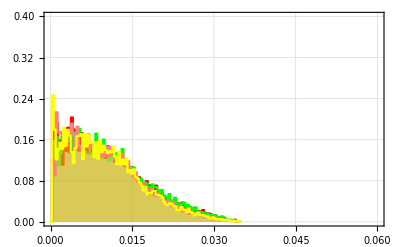
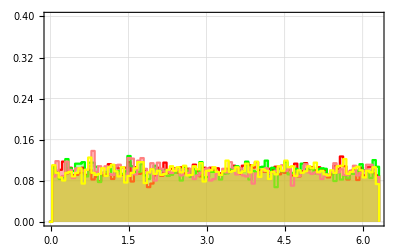
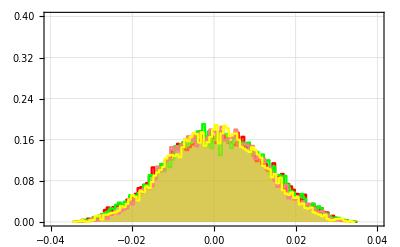
-Graphics- |  | 
-Graphics- | -Graphics- | -Graphics-
-Graphics3D- | -Graphics3D- |

```mathematica
Grid[{{MaTeX["r_z = 0,\, p = 0.3", Preamble->{"\\usepackage{newtxmath}"}], SpanFromLeft, SpanFromLeft}, 
	  Table[Show[cylPlotsMCR0Pp3[[i]], cylPlotsBrR0Pp3[[i]]], {i,3}], 
	  {visualizeBipartiteSystem[sampleR0Pp3[[1;;2000]]], visualizeBipartiteSystem[brutalsR0Pp3[[1;;2000]], {Pink,Yellow}], generalLegend}
}, ItemSize->Full]
```

```mathematica
(*Pequeña prueba:*)
cylPlots2R0Pp3BRUTAL = tripleCylindricalPlot2[brutalsR0Pp3, 0., {Pink, Yellow}, {{0,0.04}, {0, 2 Pi}, {-0.04, 0.04}}];
cylPlots2R0Pp3MC = tripleCylindricalPlot2[sampleR0Pp3, 0., {Red, Green}, {{0,0.04}, {0, 2 Pi}, {-0.04, 0.04}}, {Automatic, Automatic, 20}];
```

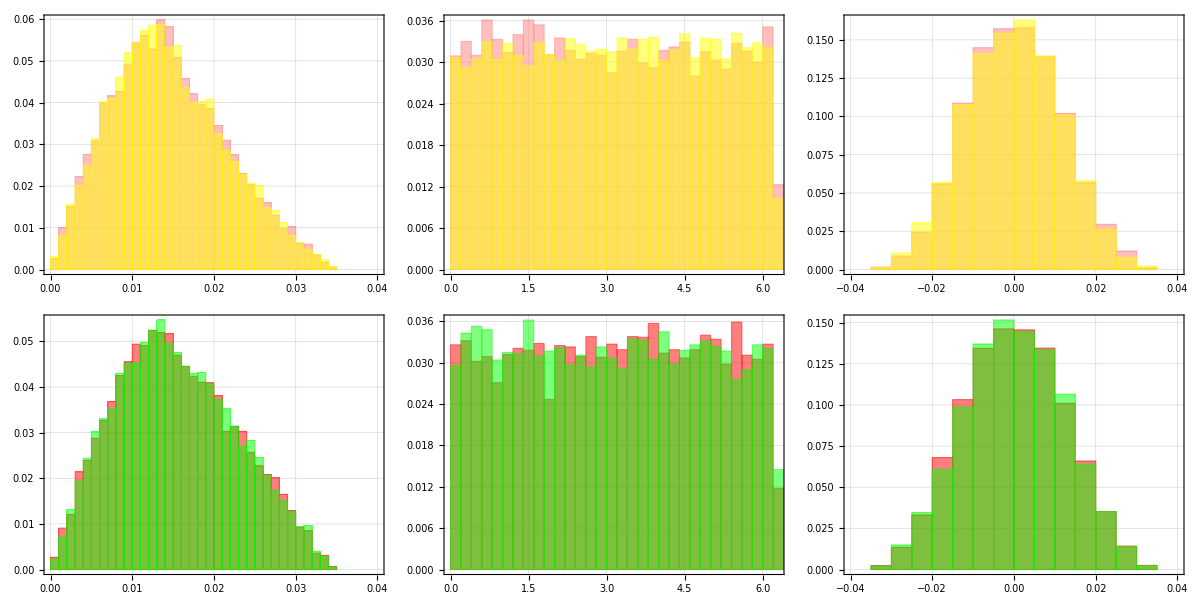

```mathematica
Grid[{cylPlots2R0Pp3BRUTAL, cylPlots2R0Pp3MC}]
```

```mathematica
Export["mcRESgood_R0Pp3.pdf", %86]
```

mcRESgood_R0Pp3.pdf

```mathematica
avgStateR0Pp3 = preimageMean[sampleR0Pp3];
avgStateRoPp3ROUND = numForm[avgStateR0Pp3, 2]; (*sólo por presentación*)
avgStateR0Pp3EXACT = ρaverageTwoQubitsbasiscomp[0.3, 0.];
avgStateR0Pp3BRUTAL = preimageMean[brutalsR0Pp3];
fidelity[avgStateR0Pp3, avgStateR0Pp3BRUTAL]
```

0.995181

```mathematica
avgStateRoPp3ROUND//MatrixForm
```

(0.23+0. ⅈ | -0.0015-0.0023 ⅈ | -0.00047-0.00013 ⅈ | -0.0013+0.0018 ⅈ
-0.0015+0.0023 ⅈ | 0.27+0. ⅈ | -0.029-0.0025 ⅈ | 0.00052+0.000095 ⅈ
-0.00047+0.00013 ⅈ | -0.029+0.0025 ⅈ | 0.27+0. ⅈ | 0.0015+0.0024 ⅈ
-0.0013-0.0018 ⅈ | 0.00052-0.000095 ⅈ | 0.0015-0.0024 ⅈ | 0.23+0. ⅈ)

```mathematica
TeXForm[avgStateRoPp3ROUND]
```

\left(
\begin{array}{cccc}
 0.23+0. i & -0.0015-0.0023 i & -0.00047-0.00013 i & -0.0013+0.0018 i \\
 -0.0015+0.0023 i & 0.27+0. i & -0.029-0.0025 i & 0.00052+0.000095 i \\
 -0.00047+0.00013 i & -0.029+0.0025 i & 0.27+0. i & 0.0015+0.0024 i \\
 -0.0013-0.0018 i & 0.00052-0.000095 i & 0.0015-0.0024 i & 0.23+0. i \\
\end{array}
\right)

#### Visualizaciones y promedio para p = 0.5

```mathematica
(*distribución de los puntos. Comparación con el brutal:*)
brutalsR0Pp5 = ketsToDensity[Get["/media/storage/ciencia/investigacion/adanerick/muestras_de_edos/pureBrutalStates/pureHaarStates_n=10000_p=0.5_rz=0.m"]];
cylPlotsBrR0Pp5 = tripleCylindricalPlot[brutalsR0Pp5, targets[[1]], 100, 100, 100, {Pink, Yellow}, {0,0.3}, {0,2 Pi}, {-0.3,0.3}, {0., 1}];
cylPlotsMCR0Pp5 = tripleCylindricalPlot[sampleR0Pp5, targets[[1]], 100, 100, 100, {Red, Green}, {0,0.3}, {0,2 Pi}, {-0.3,0.3}, {0., 1}];
```

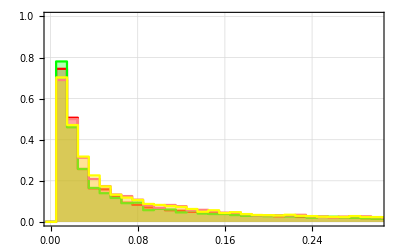
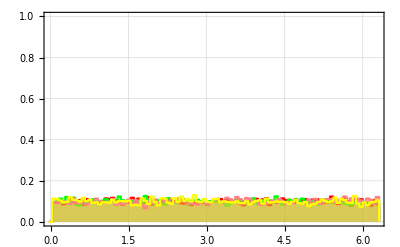
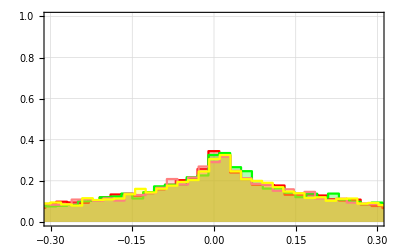
-Graphics- |  | 
-Graphics- | -Graphics- | -Graphics-
-Graphics3D- | -Graphics3D- |

```mathematica
Grid[{{MaTeX["r_z = 0,\, p = 0.5"], SpanFromLeft, SpanFromLeft}, 
	  Table[Show[cylPlotsMCR0Pp5[[i]], cylPlotsBrR0Pp5[[i]]], {i,3}], 
	  {visualizeBipartiteSystem[sampleR0Pp5[[1;;2000]]], visualizeBipartiteSystem[brutalsR0Pp5[[1;;2000]], {Pink,Yellow}], generalLegend}
}, ItemSize->Full]
```

```mathematica
(*Prqueña prueba*)
cylPlots2R0Pp5BRUTAL = tripleCylindricalPlot2[brutalsR0Pp5, 0., {Pink, Yellow}];
cylPlots2R0Pp5MC = tripleCylindricalPlot2[sampleR0Pp5, 0., {Red, Green}];
```

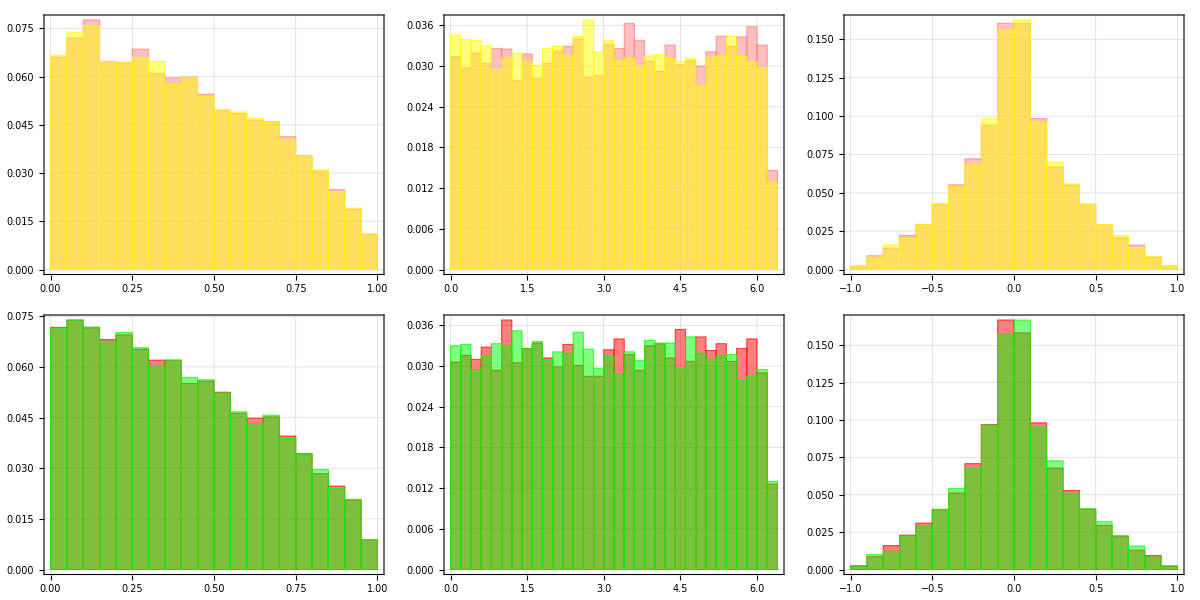

```mathematica
Grid[{cylPlots2R0Pp5BRUTAL, cylPlots2R0Pp5MC}]
```

```mathematica
Export["mcRESgood_R0Pp5.pdf", %91]
```

mcRESgood_R0Pp5.pdf

```mathematica
avgStateR0Pp5 = preimageMean[sampleR0Pp5];
avgStateR0Pp5ROUND = numForm[avgStateR0Pp5, 2]; (*sólo por presentación*)
(*exactAvgStateR0Pp5 = ρaverageTwoQubitsbasiscomp[0.5, 0.]; SE INDETERMINA*)
avgStateR0Pp5BRUTAL = preimageMean[brutalsR0Pp5];
fidelity[avgStateR0Pp5, avgStateR0Pp5BRUTAL]
```

0.971847

```mathematica
avgStateR0Pp5ROUND//MatrixForm
```

(0.22+0. ⅈ | 0.0016+0.00046 ⅈ | -0.00015-0.0017 ⅈ | 0.0021+0.0013 ⅈ
0.0016-0.00046 ⅈ | 0.28+0. ⅈ | -0.058+0.002 ⅈ | -0.0007-0.00016 ⅈ
-0.00015+0.0017 ⅈ | -0.058-0.002 ⅈ | 0.28+0. ⅈ | -0.00072+0.0015 ⅈ
0.0021-0.0013 ⅈ | -0.0007+0.00016 ⅈ | -0.00072-0.0015 ⅈ | 0.22+0. ⅈ)

```mathematica
TeXForm[avgStateR0Pp5ROUND]
```

\left(
\begin{array}{cccc}
 0.22+0. i & 0.0016+0.00046 i & -0.00015-0.0017 i & 0.0021+0.0013 i \\
 0.0016-0.00046 i & 0.28+0. i & -0.058+0.002 i & -0.0007-0.00016 i \\
 -0.00015+0.0017 i & -0.058-0.002 i & 0.28+0. i & -0.00072+0.0015 i \\
 0.0021-0.0013 i & -0.0007+0.00016 i & -0.00072-0.0015 i & 0.22+0. i \\
\end{array}
\right)

#### Visualizaciones y promedio para p = 0.8

```mathematica
(*distribución de los puntos. Comparación con el brutal:*)
brutalsR0Pp8 = ketsToDensity[Get["/media/storage/ciencia/investigacion/adanerick/muestras_de_edos/pureBrutalStates/pureHaarStates_n=10000_p=0.8_rz=0.m"]];
cylPlotsBrR0Pp8 = tripleCylindricalPlot[brutalsR0Pp8, targets[[1]], 100, 100, 100, {Pink, Yellow}, {0.,0.03}, {0,2 Pi}, {-0.03,0.03}, {0., 0.25}];
cylPlotsMCR0Pp8 = tripleCylindricalPlot[sampleR0Pp8, targets[[1]], 100, 100, 100, {Red, Green}, {0.,0.03}, {0,2 Pi}, {-0.03,0.03}, {0., 0.25}];
```

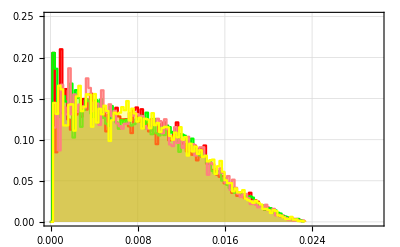
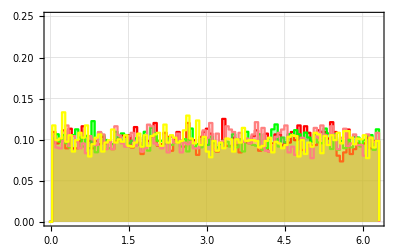
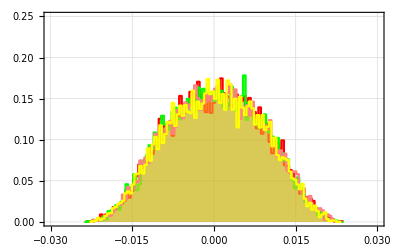
-Graphics- |  | 
-Graphics- | -Graphics- | -Graphics-
-Graphics3D- | -Graphics3D- |

```mathematica
Grid[{{MaTeX["r_z = 0,\, p = 0.8"], SpanFromLeft, SpanFromLeft}, 
	  Table[Show[cylPlotsMCR0Pp8[[i]], cylPlotsBrR0Pp8[[i]]], {i,3}], 
	  {visualizeBipartiteSystem[sampleR0Pp8[[1;;2000]]], visualizeBipartiteSystem[brutalsR0Pp8[[1;;2000]], {Pink,Yellow}], generalLegend}
}, ItemSize->Full]
```

```mathematica
(*Pequeña prueba*)
cylPlots2R0Pp8BRUTAL = tripleCylindricalPlot2[brutalsR0Pp8, 0, {Pink, Yellow}];
cylPlots2R0Pp8MC = tripleCylindricalPlot2[sampleR0Pp8, 0, {Red, Green}];
```

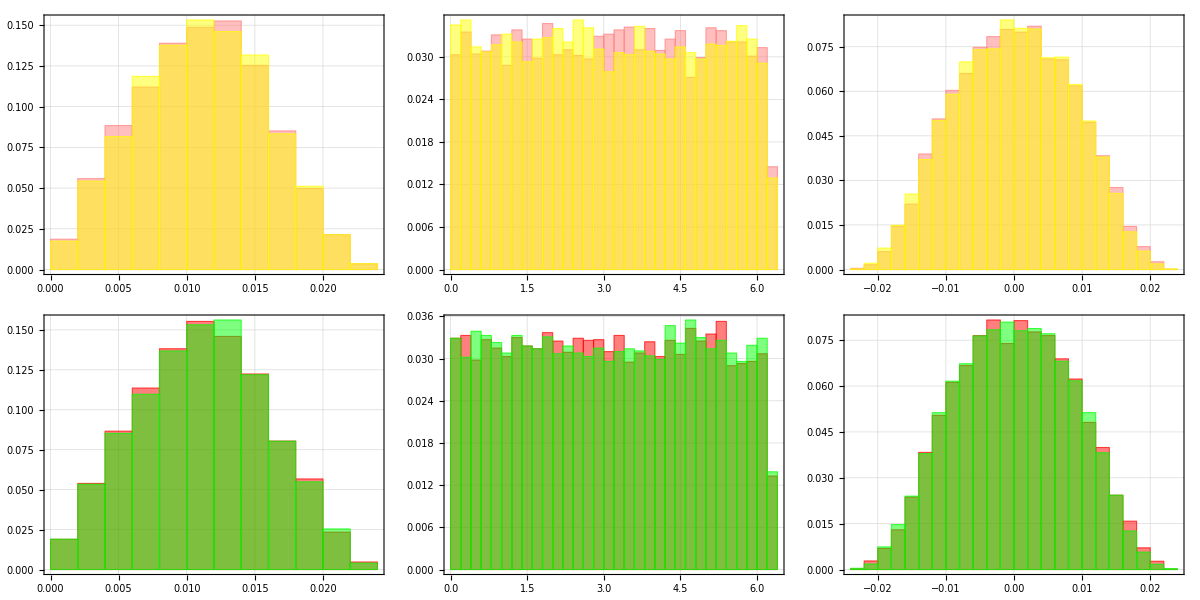

```mathematica
Grid[{cylPlots2R0Pp8BRUTAL, cylPlots2R0Pp8MC}]
```

```mathematica
Export["mcRESgood_R0Pp8.pdf", %96]
```

mcRESgood_R0Pp8.pdf

```mathematica
avgStateR0Pp8 = preimageMean[sampleR0Pp8];
avgStateR0Pp8ROUND = numForm[avgStateR0Pp8, 2]; (*sólo por presentación*)
avgStateR0Pp8EXACT = ρaverageTwoQubitsbasiscomp[0.2, 0.];
avgStateR0Pp8BRUTAL = preimageMean[brutalsR0Pp8];
fidelity[avgStateR0Pp8, avgStateR0Pp8BRUTAL]
```

0.998599

```mathematica
avgStateR0Pp8ROUND//MatrixForm
```

(0.24 | 0.0014-0.0026 ⅈ | 0.00079-0.0017 ⅈ | -0.00016+0.00099 ⅈ
0.0014+0.0026 ⅈ | 0.26 | -0.017-0.0018 ⅈ | -0.00075+0.0017 ⅈ
0.00079+0.0017 ⅈ | -0.017+0.0018 ⅈ | 0.26 | -0.0014+0.0026 ⅈ
-0.00016-0.00099 ⅈ | -0.00075-0.0017 ⅈ | -0.0014-0.0026 ⅈ | 0.24)

```mathematica
TeXForm[avgStateR0Pp8ROUND]
```

\left(
\begin{array}{cccc}
 0.24 & 0.0014-0.0026 i & 0.00079-0.0017 i & -0.00016+0.00099 i \\
 0.0014+0.0026 i & 0.26 & -0.017-0.0018 i & -0.00075+0.0017 i \\
 0.00079+0.0017 i & -0.017+0.0018 i & 0.26 & -0.0014+0.0026 i \\
 -0.00016-0.00099 i & -0.00075-0.0017 i & -0.0014-0.0026 i & 0.24 \\
\end{array}
\right)

### Target rz = 0.5

```mathematica
sampleRp5Pp3 = cleanSample[Get["initial_samples/sampleMCS_n=10000_err=0.01_paso=0.01_t=0.3_rz=0.5_p=0.3.m"][[2]], 0.5, 0.3, 0.01];
sampleRp5Pp5 = cleanSample[Get["initial_samples/sampleMCS_n=10000_err=0.01_paso=0.01_t=0.3_rz=0.5_p=0.5.m"][[2]], 0.5, 0.5, 0.01];
sampleRp5Pp8 = cleanSample[Get["initial_samples/sampleMCS_n=10000_err=0.01_paso=0.01_t=0.3_rz=0.5_p=0.8.m"][[2]], 0.5, 0.8, 0.01];
```

```mathematica
Clear[sampleRp5Pp3, sampleRp5Pp5, sampleRp5Pp8]
```

#### Visualizaciones y promedio para p = 0.3

```mathematica
(*distribución de los puntos. Comparación con el brutal:*)
brutalsRp5Pp3 = ketsToDensity[Get["/media/storage/ciencia/investigacion/adanerick/muestras_de_edos/pureBrutalStates/pureHaarStates_n=10000_p=0.3_rz=0.5.m"]];
cylPlotsBrRp5Pp3 = tripleCylindricalPlot[brutalsRp5Pp3, targets[[2]], 100, 100, 100, {Pink, Yellow}, {0., 1.}, {0,2 Pi}, {-1.1,0.6}, {0., 0.5}];
cylPlotsMCRp5Pp3 = tripleCylindricalPlot[sampleRp5Pp3, targets[[2]], 100, 100, 100, {Red, Green}, {0.,1.}, {0,2 Pi}, {-1.1,0.6}, {0., 0.5}];
```

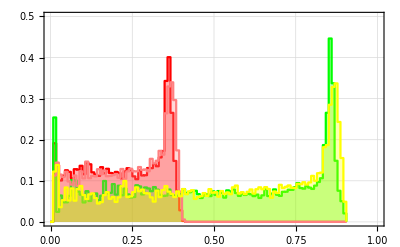
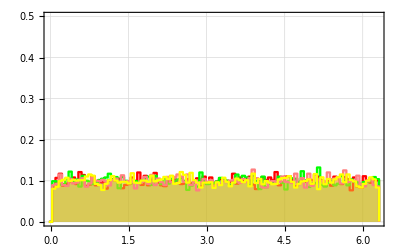
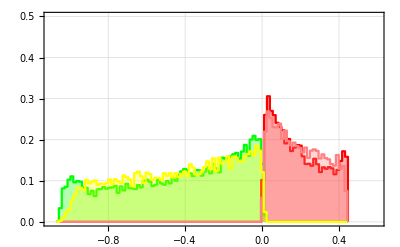
-Graphics- |  | 
-Graphics- | -Graphics- | -Graphics-
-Graphics3D- | -Graphics3D- |

```mathematica
Grid[{{MaTeX["r_z = 0.5,\, p = 0.3"], SpanFromLeft, SpanFromLeft}, 
	  Table[Show[cylPlotsMCRp5Pp3[[i]], cylPlotsBrRp5Pp3[[i]]], {i,3}], 
	  {visualizeBipartiteSystem[sampleRp5Pp3[[1;;2000]]], visualizeBipartiteSystem[brutalsRp5Pp3[[1;;2000]], {Pink,Yellow}], generalLegend}
}, ItemSize->Full]
```

```mathematica
(*Pequeña prueba*)
cylPlots2Rp5Pp3BRUTAL = tripleCylindricalPlot2[brutalsRp5Pp3, 0.5, {Pink, Yellow}, {{0,1}, {0, 2 Pi}, Full}];
cylPlots2Rp5Pp3MC = tripleCylindricalPlot2[sampleRp5Pp3, 0.5, {Red, Green}, {{0,1}, {0, 2 Pi}, Full}, {Automatic, Automatic, Automatic}];
```

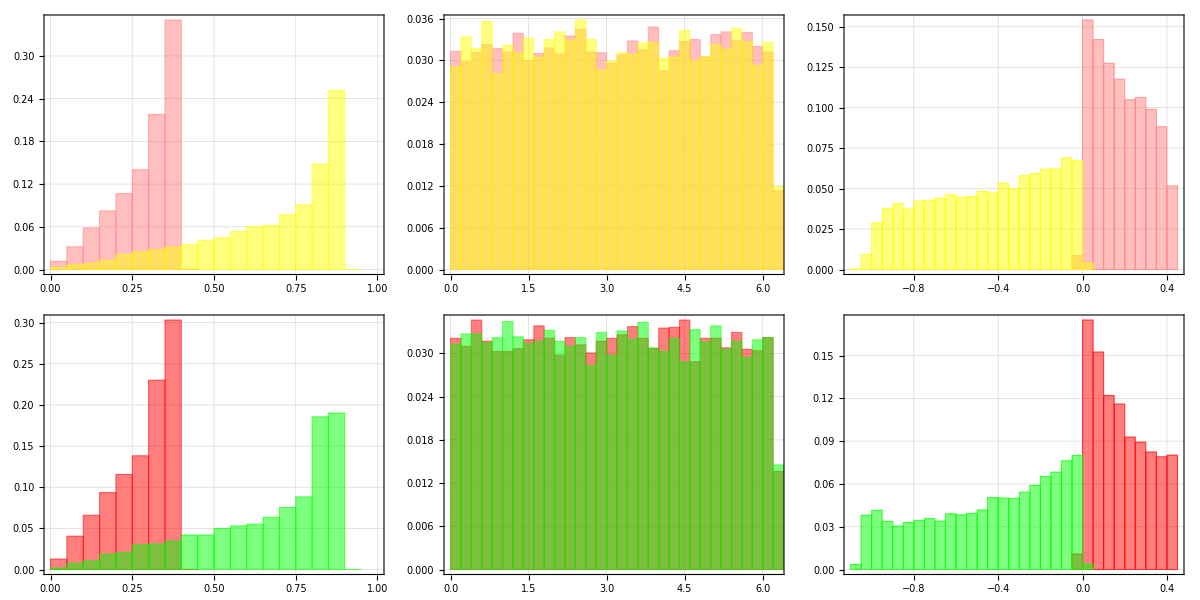

```mathematica
Grid[{cylPlots2Rp5Pp3BRUTAL, cylPlots2Rp5Pp3MC}]
```

```mathematica
Export["mcRESgood_Rp5Pp3.pdf", %105]
```

mcRESgood_Rp5Pp3.pdf

```mathematica
(*Estado promedio*)
avgStateRp5Pp3 = preimageMean[sampleRp5Pp3];
avgStateRp5Pp3ROUND = numForm[avgStateRp5Pp3, 2]; (*sólo por presentación*)
avgStateRp5Pp3EXACT = ρaverageTwoQubitsbasiscomp[0.3, 0.5];
avgStateRp5Pp3BRUTAL = preimageMean[brutalsRp5Pp3];
fidelity[avgStateRp5Pp3, avgStateRp5Pp3BRUTAL]
```

0.99956

```mathematica
avgStateRp5Pp3ROUND//MatrixForm
```

(0.47 | -0.00014+0.00094 ⅈ | 0.00085-0.0018 ⅈ | 0.004+0.0012 ⅈ
-0.00014-0.00094 ⅈ | 0.049 | -0.075+0.0009 ⅈ | 0.000021+0.0008 ⅈ
0.00085+0.0018 ⅈ | -0.075-0.0009 ⅈ | 0.37 | -0.00018-0.00045 ⅈ
0.004-0.0012 ⅈ | 0.000021-0.0008 ⅈ | -0.00018+0.00045 ⅈ | 0.11)

```mathematica
TeXForm[avgStateRp5Pp3ROUND]
```

\left(
\begin{array}{cccc}
 0.47 & -0.00014+0.00094 i & 0.00085-0.0018 i & 0.004+0.0012 i \\
 -0.00014-0.00094 i & 0.049 & -0.075+0.0009 i & 0.000021+0.0008 i \\
 0.00085+0.0018 i & -0.075-0.0009 i & 0.37 & -0.00018-0.00045 i \\
 0.004-0.0012 i & 0.000021-0.0008 i & -0.00018+0.00045 i & 0.11 \\
\end{array}
\right)

#### Visualizaciones y promedio para p = 0.5

```mathematica
(*distribución de los puntos. Comparación con el brutal:*)
brutalsRp5Pp5 = ketsToDensity[Get["/media/storage/ciencia/investigacion/adanerick/muestras_de_edos/pureBrutalStates/pureHaarStates_n=10000_p=0.5_rz=0.5.m"]];
cylPlotsBrRp5Pp5 = tripleCylindricalPlot[brutalsRp5Pp5, targets[[2]], 100, 100, 100, {Pink, Yellow}, {0., 1.}, {0, 2 Pi}, {-0.04,0.04}, {0., 0.3}];
cylPlotsMCRp5Pp5 = tripleCylindricalPlot[sampleRp5Pp5, targets[[2]], 100, 100, 100, {Red, Green}, {0.,1.}, {0, 2 Pi}, {-0.04,0.04}, {0., 0.3}];
```

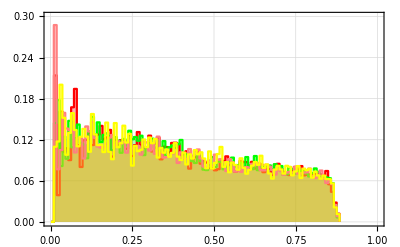
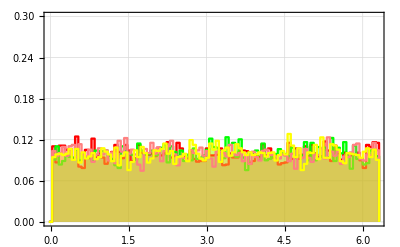
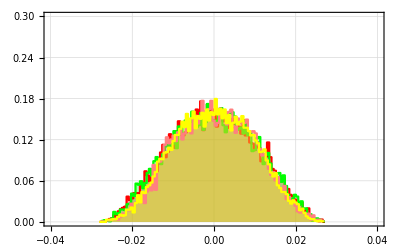
-Graphics- |  | 
-Graphics- | -Graphics- | -Graphics-
-Graphics3D- | -Graphics3D- |

```mathematica
Grid[{{MaTeX["r_z = 0.5,\, p = 0.5"], SpanFromLeft, SpanFromLeft}, 
	  Table[Show[cylPlotsMCRp5Pp5[[i]], cylPlotsBrRp5Pp5[[i]]], {i,3}], 
	  {visualizeBipartiteSystem[sampleRp5Pp5[[1;;2000]]], visualizeBipartiteSystem[brutalsRp5Pp5[[1;;2000]], {Pink,Yellow}], generalLegend}
}, ItemSize->Full]
```

```mathematica
(*Pequeña prueba:*)
cylPlots2Rp5Pp5BRUTAL = tripleCylindricalPlot2[brutalsRp5Pp5, 0.5, {Pink, Yellow}, {{0,0.9}, {0, 2 Pi}, {-0.03, 0.03}}];
cylPlots2Rp5Pp5MC = tripleCylindricalPlot2[sampleRp5Pp5, 0.5, {Red, Green}, {{0,0.9}, {0, 2 Pi}, {-0.03, 0.03}}];
```

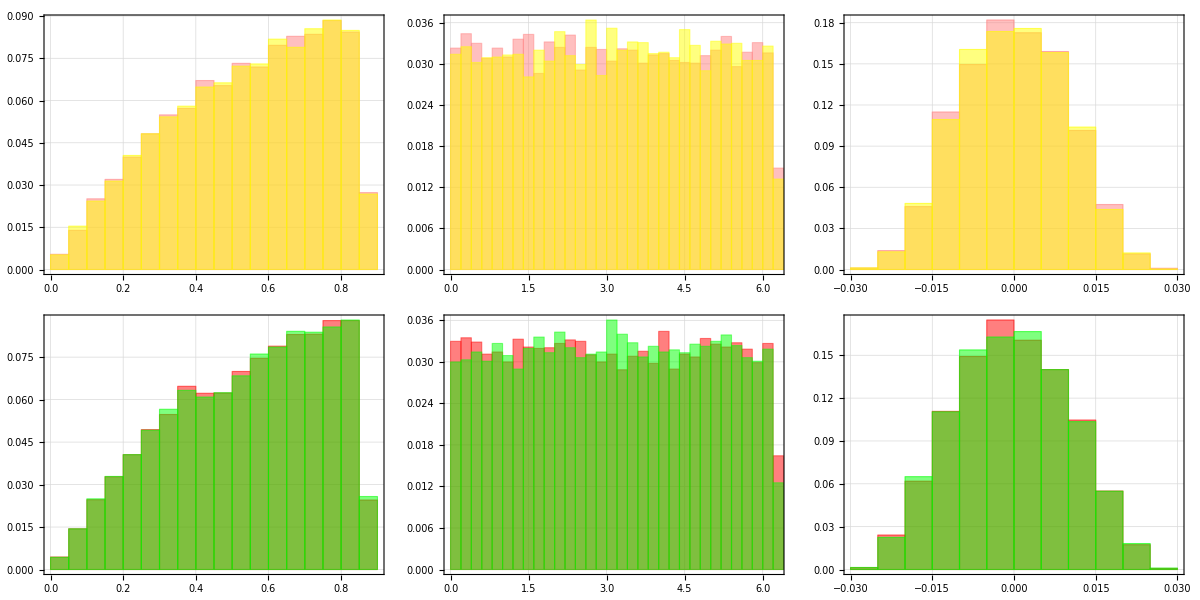

```mathematica
Grid[{cylPlots2Rp5Pp5BRUTAL, cylPlots2Rp5Pp5MC}]
```

```mathematica
Export["mcRESgood_Rp5Pp5.pdf", %110]
```

mcRESgood_Rp5Pp5.pdf

Acá se observa una diferencia en el histograma Z, donde los picos del MC son mucho más altos que los del brutal.

```mathematica
avgStateRp5Pp5 = preimageMean[sampleRp5Pp5];
avgStateRp5Pp5ROUND = numForm[avgStateRp5Pp5, 2]; (*sólo por presentación*)
avgStateRp5Pp5EXACT = ρaverageTwoQubitsbasiscomp[0.5, 0.5];
avgStateRp5Pp5BRUTAL = preimageMean[brutalsRp5Pp5];
fidelity[avgStateRp5Pp5, avgStateRp5Pp5BRUTAL]
```

0.999615

```mathematica
avgStateRp5Pp5ROUND//MatrixForm
```

(0.62 | 0.0021-0.0025 ⅈ | -0.0024+0.0024 ⅈ | -0.0015+0.00091 ⅈ
0.0021+0.0025 ⅈ | 0.13 | -0.13-(6.3×10^-6) ⅈ | -0.00046-0.00072 ⅈ
-0.0024-0.0024 ⅈ | -0.13+(6.3×10^-6) ⅈ | 0.13 | 0.00062+0.00069 ⅈ
-0.0015-0.00091 ⅈ | -0.00046+0.00072 ⅈ | 0.00062-0.00069 ⅈ | 0.12)

```mathematica
TeXForm[avgStateRp5Pp5ROUND]
```

\left(
\begin{array}{cccc}
 0.62 & 0.0021-0.0025 i & -0.0024+0.0024 i & -0.0015+0.00091 i \\
 0.0021+0.0025 i & 0.13 & -0.13-\left(6.3\times 10^{-6}\right) i & -0.00046-0.00072 i \\
 -0.0024-0.0024 i & -0.13+\left(6.3\times 10^{-6}\right) i & 0.13 & 0.00062+0.00069 i \\
 -0.0015-0.00091 i & -0.00046+0.00072 i & 0.00062-0.00069 i & 0.12 \\
\end{array}
\right)

#### Visualizaciones y promedios para p = 0.8

```mathematica
(*distribución de los puntos. Comparación con el brutal:*)
brutalsRp5Pp8 = ketsToDensity[Get["/media/storage/ciencia/investigacion/adanerick/muestras_de_edos/pureBrutalStates/pureHaarStates_n=10000_p=0.8_rz=0.5.m"]];
cylPlotsBrRp5Pp8 = tripleCylindricalPlot[brutalsRp5Pp8, targets[[2]], 200, 200, 200, {Pink, Yellow}, {0.,0.8}, {0,2 Pi}, {-1.5, 0.5}, {0., 0.4}];
cylPlotsMCRp5Pp8 = tripleCylindricalPlot[sampleRp5Pp8, targets[[2]], 200, 200, 200, {Red, Green}, {0.,0.8}, {0,2 Pi}, {-1.5,0.5}, {0., 0.4}];
```

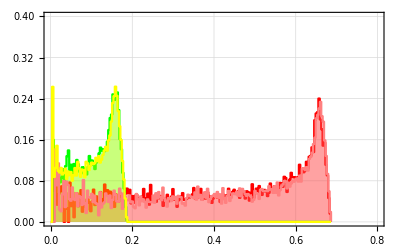
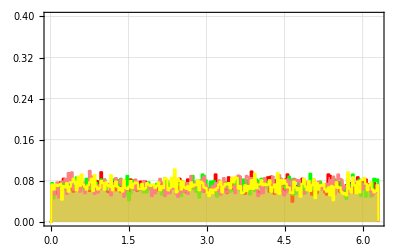
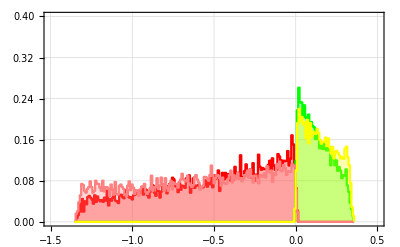
-Graphics- |  | 
-Graphics- | -Graphics- | -Graphics-
-Graphics3D- | -Graphics3D- |

```mathematica
Grid[{{MaTeX["r_z = 0.5,\, p = 0.8"], SpanFromLeft, SpanFromLeft}, 
	  Table[Show[cylPlotsMCRp5Pp8[[i]], cylPlotsBrRp5Pp8[[i]]], {i,3}], 
	  {visualizeBipartiteSystem[sampleRp5Pp8[[1;;2000]]], visualizeBipartiteSystem[brutalsRp5Pp8[[1;;2000]], {Pink,Yellow}], generalLegend}
}, ItemSize->Full]
```

```mathematica
(*Pequeña prueba*)
cylPlots2Rp5Pp8BRUTAL = tripleCylindricalPlot2[brutalsRp5Pp8, 0.5, {Pink, Yellow}];
cylPlots2Rp5Pp8MC = tripleCylindricalPlot2[sampleRp5Pp8, 0.5, {Red, Green}];
```

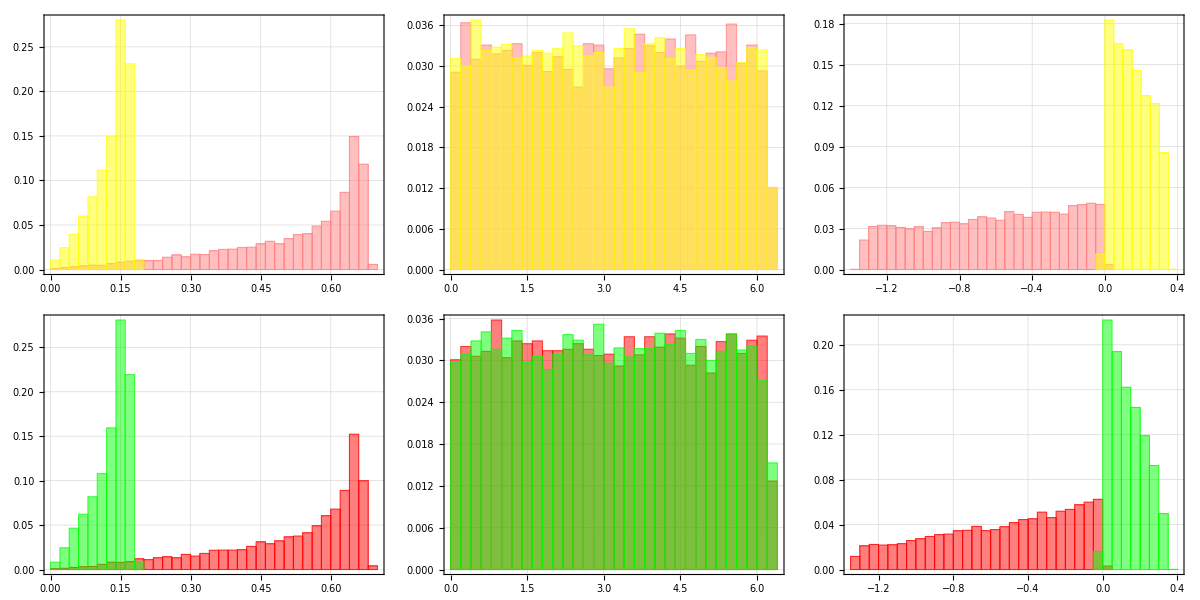

```mathematica
Grid[{cylPlots2Rp5Pp8BRUTAL, cylPlots2Rp5Pp8MC}]
```

```mathematica
Export["mcRESgood_Rp5Pp8.pdf", %115]
```

mcRESgood_Rp5Pp8.pdf

```mathematica
avgStateRp5Pp8 = preimageMean[sampleRp5Pp8];
avgStateRp5Pp8ROUND = numForm[avgStateRp5Pp8, 2]; (*sólo por presentación*)
avgStateRp5Pp83EXACT = swapGate.ρaverageTwoQubitsbasiscomp[0.2, 0.5].swapGate;
avgStateRp5Pp8BRUTAL = preimageMean[brutalsRp5Pp8];
fidelity[avgStateRp5Pp8, avgStateRp5Pp8BRUTAL]
```

0.996793

```mathematica
avgStateRp5Pp8ROUND//MatrixForm
```

(0.41 | 0.00057+0.00048 ⅈ | -0.00033-0.00065 ⅈ | 0.00035-0.00077 ⅈ
0.00057-0.00048 ⅈ | 0.41 | -0.028-0.000044 ⅈ | 0.00014+0.00059 ⅈ
-0.00033+0.00065 ⅈ | -0.028+0.000044 ⅈ | 0.075 | 0.000077+0.000011 ⅈ
0.00035+0.00077 ⅈ | 0.00014-0.00059 ⅈ | 0.000077-0.000011 ⅈ | 0.11)

```mathematica
TeXForm[avgStateRp5Pp8ROUND]
```

\left(
\begin{array}{cccc}
 0.41 & 0.00057+0.00048 i & -0.00033-0.00065 i & 0.00035-0.00077 i \\
 0.00057-0.00048 i & 0.41 & -0.028-0.000044 i & 0.00014+0.00059 i \\
 -0.00033+0.00065 i & -0.028+0.000044 i & 0.075 & 0.000077+0.000011 i \\
 0.00035+0.00077 i & 0.00014-0.00059 i & 0.000077-0.000011 i & 0.11 \\
\end{array}
\right)

### Target rz = 0.8

```mathematica
sampleRp8Pp3 = cleanSample[Get["initial_samples/sampleMCS_n=10000_err=0.01_paso=0.01_t=0.3_rz=0.8_p=0.3.m"][[2]], 0.8, 0.3, 0.01];
sampleRp8Pp5 = cleanSample[Get["initial_samples/sampleMCS_n=10000_err=0.01_paso=0.01_t=0.3_rz=0.8_p=0.5.m"][[2]], 0.8, 0.5, 0.01];
sampleRp8Pp8 = cleanSample[Get["initial_samples/sampleMCS_n=10000_err=0.01_paso=0.01_t=0.3_rz=0.8_p=0.8.m"][[2]], 0.8, 0.8, 0.01];
```

```mathematica
Clear[sampleRp8Pp3, sampleRp8Pp5, sampleRp8Pp8]
```

#### Visualizaciones y promedio para p = 0.3

```mathematica
(*distribución de los puntos. Comparación con el brutal:*)
brutalsRp8Pp3 = ketsToDensity[Get["/media/storage/ciencia/investigacion/adanerick/muestras_de_edos/pureBrutalStates/pureHaarStates_n=10000_p=0.3_rz=0.8.m"]];
cylPlotsBrRp8Pp3 = tripleCylindricalPlot[brutalsRp8Pp3, targets[[3]], 100, 100, 100, {Pink, Yellow}, {0.,1}, {0,2 Pi}, {-0.4, 0.2}, {0., 0.6}];
cylPlotsMCRp8Pp3 = tripleCylindricalPlot[sampleRp8Pp3, targets[[3]], 100, 100, 100, {Red, Green}, {0.,1}, {0,2 Pi}, {-0.4,0.2}, {0., 0.6}];
```

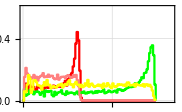
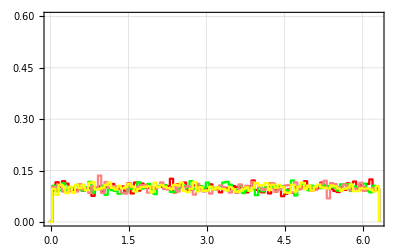
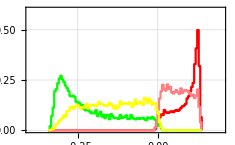
r_z = 0.8, p = 0.3 |  | 
-Graphics- | -Graphics- | -Graphics-
-Graphics3D- | -Graphics3D- |

```mathematica
Grid[{{Text["r_z = 0.8, p = 0.3"], SpanFromLeft, SpanFromLeft}, 
	  Table[Show[cylPlotsMCRp8Pp3[[i]], cylPlotsBrRp8Pp3[[i]]], {i,3}], 
	  {visualizeBipartiteSystem[sampleRp8Pp3[[1;;2000]]], visualizeBipartiteSystem[brutalsRp8Pp3[[1;;2000]], {Pink,Yellow}], generalLegend}
}]
```

```mathematica
(*Pequeña prueba*)
cylPlots2Rp8Pp3BRUTAL = tripleCylindricalPlot2[brutalsRp8Pp3, 0.8, {Pink, Yellow}, {Full, Full, Full}, {100, 100, 100}];
cylPlots2Rp8Pp3MC = tripleCylindricalPlot2[sampleRp8Pp3, 0.8, {Red, Green}, {Full, Full, Full}, {100, 100, 100}];
```

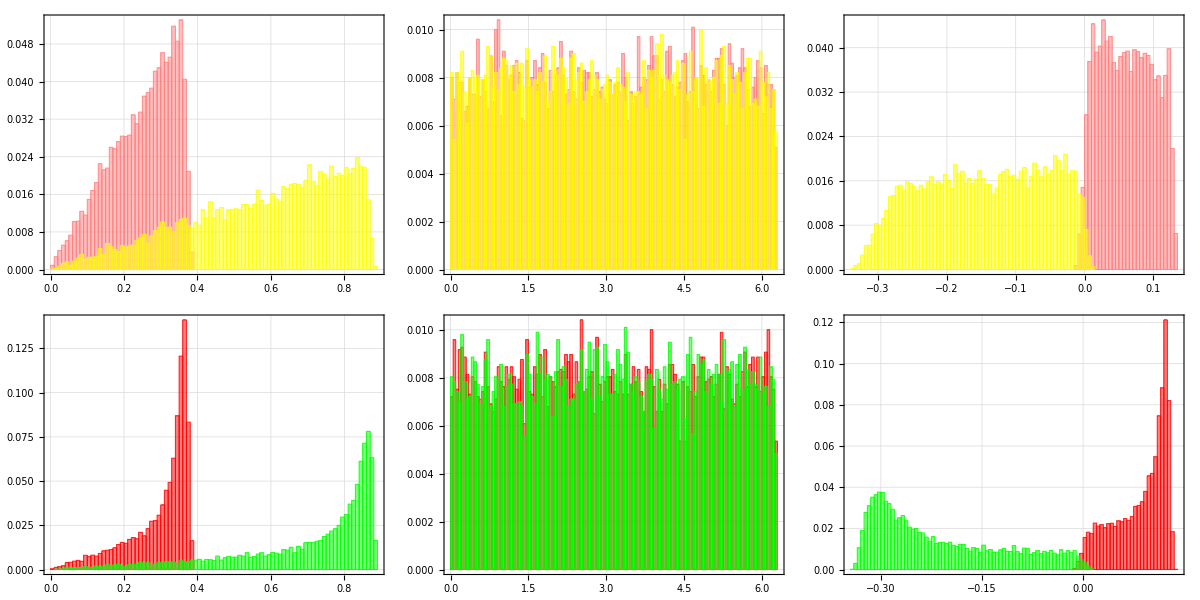

```mathematica
Grid[{cylPlots2Rp8Pp3BRUTAL, cylPlots2Rp8Pp3MC}]
```

Para este caso, los histogramas R y Z parecen compartir la región, pero el MC tiene unos picos sobresalientes.

```mathematica
avgStateRp8Pp3 = preimageMean[sampleRp8Pp3];
(*avgRptoOchoPptoTresRound = numForm[avgRptoOchoPptoTres, 2]; (*sólo por presentación*)*)
exactAvgStateRp8Pp3 = ρaverageTwoQubitsbasiscomp[0.3, 0.8];
fidelity[avgStateRp8Pp3, exactAvgStateRp8Pp3]
```

0.992677

```mathematica
avgStateRp8Pp3//MatrixForm
exactAvgStateRp8Pp3//MatrixForm
```

(0.76504 | 0.00054667-0.000988642 ⅈ | -0.00177829+0.00234079 ⅈ | -0.000745154-0.000234333 ⅈ
0.00054667+0.000988642 ⅈ | 0.0245082 | -0.0620166+0.0000248569 ⅈ | 0.0000557117+0.0000227788 ⅈ
-0.00177829-0.00234079 ⅈ | -0.0620166-0.0000248569 ⅈ | 0.178355 | 0.0000763751-0.000111969 ⅈ
-0.000745154+0.000234333 ⅈ | 0.0000557117-0.0000227788 ⅈ | 0.0000763751+0.000111969 ⅈ | 0.0320966)

(0.806944 | 0. | 0. | 0.
0. | 0.0208333 | -0.046627 | 0.
0. | -0.046627 | 0.124008 | 0.
0. | 0. | 0. | 0.0482143)

#### Visualizaciones y promedio para p = 0.5

```mathematica
(*distribución de los puntos. Comparación con el brutal:*)
brutalsRp8Pp5 = ketsToDensity[Get["/media/storage/ciencia/investigacion/adanerick/muestras_de_edos/pureBrutalStates/pureHaarStates_n=10000_p=0.5_rz=0.8.m"]];
cylPlotsBrRp8Pp5 = tripleCylindricalPlot[brutalsRp8Pp5, targets[[3]], 100, 100, 100, {Pink, Yellow}, {0.,0.7}, {0,2 Pi}, {-0.1, 0.1}, {0., 0.3}];
cylPlotsMCRp8Pp5 = tripleCylindricalPlot[sampleRp8Pp5, targets[[3]], 100, 100, 100, {Red, Green}, {0.,0.7}, {0,2 Pi}, {-0.1,0.1}, {0., 0.3}];
```

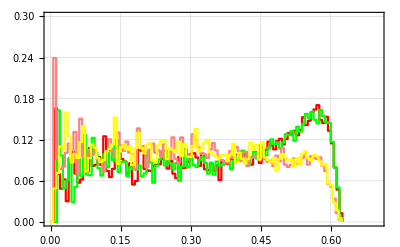
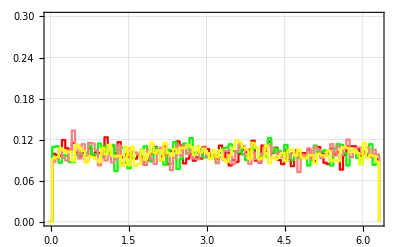
r_z = 0.8, p = 0.5 |  | 
-Graphics- | -Graphics- | -Graphics-
-Graphics3D- | -Graphics3D- |

```mathematica
Grid[{{Text["r_z = 0.8, p = 0.5"], SpanFromLeft, SpanFromLeft}, 
	  Table[Show[cylPlotsMCRp8Pp5[[i]], cylPlotsBrRp8Pp5[[i]]], {i,3}], 
	  {visualizeBipartiteSystem[sampleRp8Pp5[[1;;2000]]], visualizeBipartiteSystem[brutalsRp8Pp5[[1;;2000]], {Pink,Yellow}], generalLegend}
}]
```

```mathematica
(*Pequña prueba*)
cylPlots2Rp8Pp5BRUTAL = tripleCylindricalPlot2[brutalsRp8Pp5, 0.8, {Pink, Yellow}, {{0, 0.65}, {0, 2 Pi}, {-0.015, 0.02}}, {50,50,50}];
cylPlots2Rp8Pp5MC = tripleCylindricalPlot2[sampleRp8Pp5, 0.8, {Red, Green}, {{0, 0.65}, {0, 2 Pi}, {-0.015, 0.02}}, {50,50,50}];
```

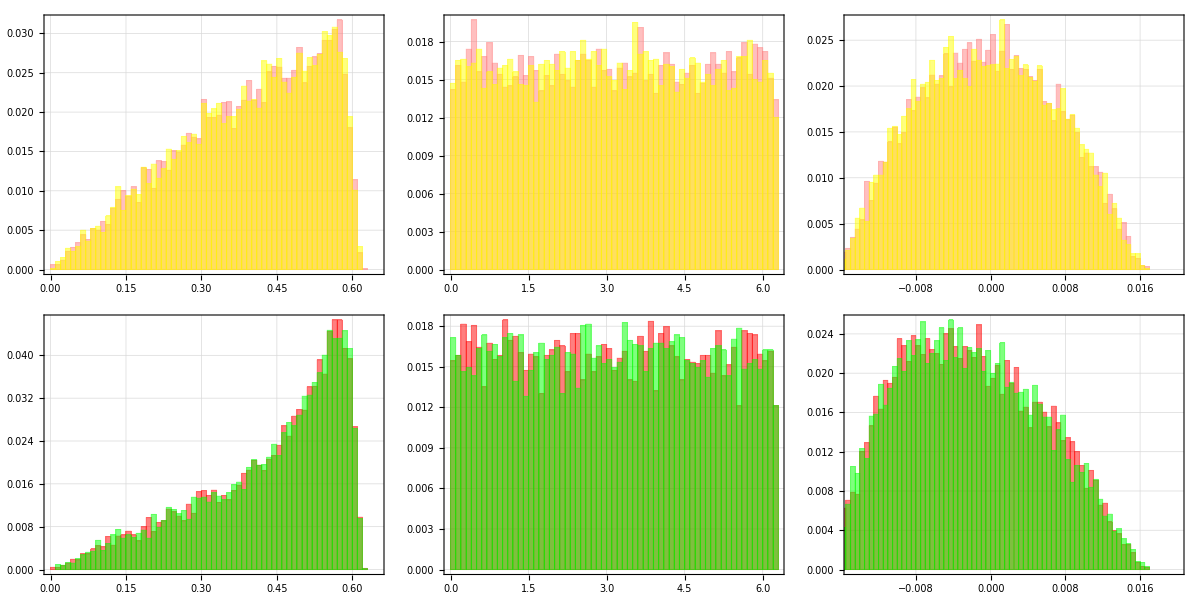

```mathematica
Grid[{cylPlots2Rp8Pp5BRUTAL, cylPlots2Rp8Pp5MC}]
```

```mathematica
avgStateRp8Pp5 = preimageMean[sampleRp8Pp5];
(*avgRptoOchoPptoCincoRound = numForm[avgRptoOchoPptoCinco, 2]; (*sólo por presentación*)*)
exactAvgStateRp8Pp5 = ρaverageTwoQubitsbasiscomp[0.5, 0.8];
fidelity[avgStateRp8Pp5, exactAvgStateRp8Pp5]
```

0.997953

```mathematica
avgStateRp8Pp5//MatrixForm
exactAvgStateRp8Pp5//MatrixForm
```

(0.837088 | 0.00125481-0.00128469 ⅈ | -0.00151566+0.0011373 ⅈ | -0.00110832-0.000903682 ⅈ
0.00125481+0.00128469 ⅈ | 0.0616664 | -0.061491+0.0000313907 ⅈ | -0.000228977+0.000142368 ⅈ
-0.00151566-0.0011373 ⅈ | -0.061491-0.0000313907 ⅈ | 0.0616669 | 0.000278788-0.0000839389 ⅈ
-0.00110832+0.000903682 ⅈ | -0.000228977-0.000142368 ⅈ | 0.000278788+0.0000839389 ⅈ | 0.0395784)

(0.85 | 0. | 0. | 0.
0. | 0.05 | -0.05 | 0.
0. | -0.05 | 0.05 | 0.
0. | 0. | 0. | 0.05)

El tercer elemento de la diagonal en ambos es el que más difiere.

#### Visualizaciones y promedio para p = 0.8

```mathematica
(*distribución de los puntos. Comparación con el brutal:*)
brutalsRp8Pp8 = ketsToDensity[Get["/media/storage/ciencia/investigacion/adanerick/muestras_de_edos/pureBrutalStates/pureHaarStates_n=10000_p=0.8_rz=0.8.m"]];
cylPlotsBrRp8Pp8 = tripleCylindricalPlot[brutalsRp8Pp8, targets[[3]], 100, 100, 100, {Pink, Yellow}, {0.,1.1}, {0,2 Pi}, {-0.8, 0.3}, {0., 0.6}];
cylPlotsMCRp8Pp8 = tripleCylindricalPlot[sampleRp8Pp8, targets[[3]], 100, 100, 100, {Red, Green}, {0.,1.1}, {0,2 Pi}, {-0.8,0.3}, {0., 0.6}];
```

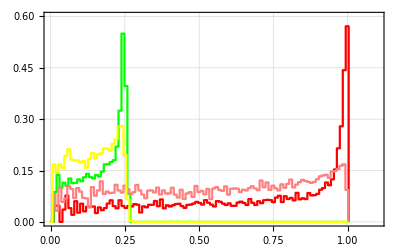
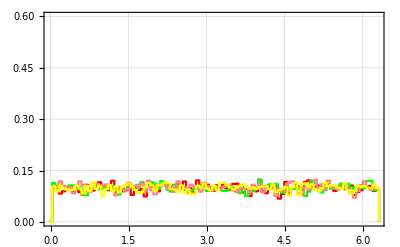
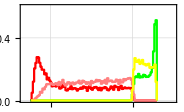
-Graphics- |  | 
-Graphics- | -Graphics- | -Graphics-
-Graphics3D- | -Graphics3D- |

```mathematica
Grid[{{MaTeX["r_z = 0.8,\, p = 0.8"], SpanFromLeft, SpanFromLeft}, 
	  Table[Show[cylPlotsMCRp8Pp8[[i]], cylPlotsBrRp8Pp8[[i]]], {i,3}], 
	  {visualizeBipartiteSystem[sampleRp8Pp8[[1;;5000]]], visualizeBipartiteSystem[brutalsRp8Pp8[[1;;2000]], {Pink,Yellow}], generalLegend}
}, ItemSize->Full]
```

```mathematica
(*Pequeña prueba*)
cylPlots2Rp8Pp8BRUTAL = tripleCylindricalPlot2[brutalsRp8Pp8, 0.8, {Pink, Yellow}, {{0,1}, {0, 2 Pi}, {-0.8, 0.25}}, {100,100,100}];
cylPlots2Rp8Pp8MC = tripleCylindricalPlot2[sampleRp8Pp8, 0.8, {Red, Green}, {{0,1}, {0, 2 Pi}, {-0.8, 0.25}}, {100,100,100}];
```

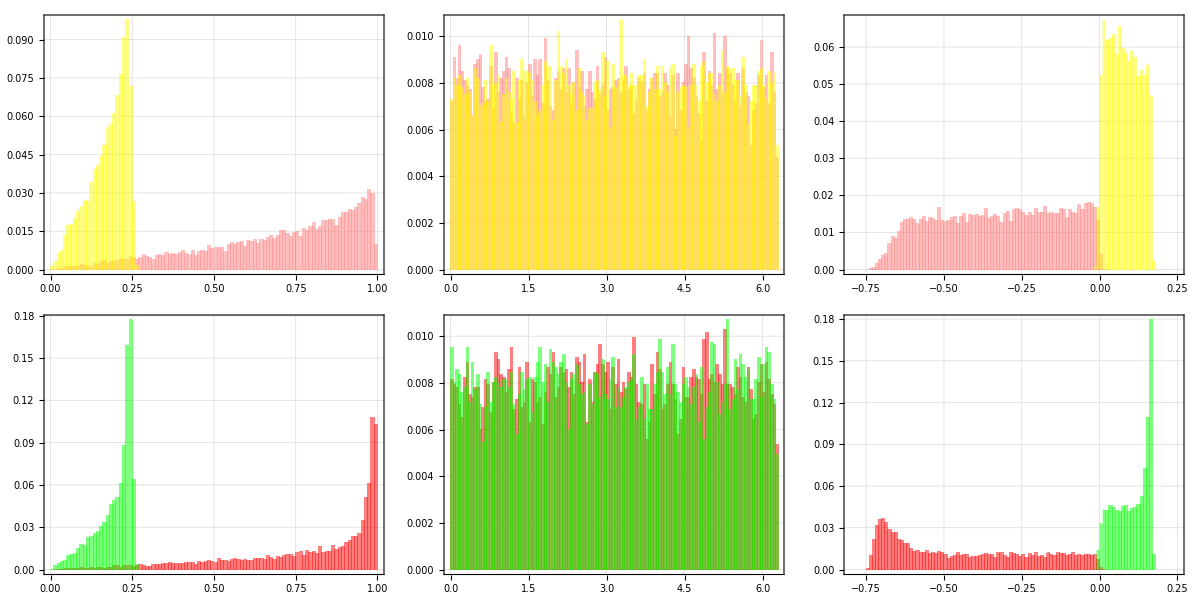

```mathematica
Grid[{cylPlots2Rp8Pp8BRUTAL, cylPlots2Rp8Pp8MC}]
```

```mathematica
Export["mcsRESweird_Rp8Pp8.pdf", %29]
```

mcsRESweird_Rp8Pp8.pdf

Al parecer, los histogramas también “comparten regiones”, pero el MC tiene picos considerables de nuevo.

```mathematica
avgStateRp8Pp8 = preimageMean[sampleRp8Pp8];
(*avgRptoOchoPptoOchoRound = numForm[avgRptoOchoPptoOcho, 2]; (*sólo por presentación*)*)
avgStateRp8Pp8EXACT = swapGate.ρaverageTwoQubitsbasiscomp[0.2, 0.8].swapGate;
avgStateRp8Pp8BRUTAL = preimageMean[brutalsRp8Pp8];
fidelity[avgStateRp8Pp8, avgStateRp8Pp8BRUTAL]
```

0.993755

```mathematica
avgStateRp8Pp8//MatrixForm
exactAvgStateRp8Pp8//MatrixForm
brutalAvgStateRp8Pp8//MatrixForm
```

(0.653257 | 0.000635583-0.000113379 ⅈ | -0.000238066-0.000146169 ⅈ | 0.000530113-0.000632769 ⅈ
0.000635583+0.000113379 ⅈ | 0.300361 | -0.0470374-0.000110472 ⅈ | 0.0000143336+0.000209424 ⅈ
-0.000238066+0.000146169 ⅈ | -0.0470374+0.000110472 ⅈ | 0.0136094 | 0.000175737+0.0000166093 ⅈ
0.000530113+0.000632769 ⅈ | 0.0000143336-0.000209424 ⅈ | 0.000175737-0.0000166093 ⅈ | 0.032773)

(0.722852 | 0. | 0. | 0.
0. | 0.0146484 | -0.0400391 | 0.
0. | -0.0400391 | 0.217773 | 0.
0. | 0. | 0. | 0.0447266)

(0.723379+0. ⅈ | 0.00206448-0.00162424 ⅈ | -0.000695939+0.0000858339 ⅈ | -0.000236596-0.000472493 ⅈ
0.00206448+0.00162424 ⅈ | 0.216937+0. ⅈ | -0.0399407-0.000239821 ⅈ | 0.000235772+0.000329745 ⅈ
-0.000695939-0.0000858339 ⅈ | -0.0399407+0.000239821 ⅈ | 0.0146986+0. ⅈ | -0.000139763-0.0000705779 ⅈ
-0.000236596+0.000472493 ⅈ | 0.000235772-0.000329745 ⅈ | -0.000139763+0.0000705779 ⅈ | 0.0449849+0. ⅈ)

De nuevo, parece que los dos elementos internos de la diagonal están al revés. Puede que por eso sea el bajón en fidelidad.

### Pequeña prueba

Los casos con r_z = 0.5, 0.8 y p = 0.8 presentan algo curioso: los elementos 2 y 3 de la diagonal del edo promedio numérico parecen estar al revés respecto de los del exacto. Veamos con otros edos promedio obtenidos con otros métodos

```mathematica
brutalAvgRp5Pp8 = preimageMean[brutalsRp5Pp8];
brutalAvgRp8Pp8 = preimageMean[brutalsRp8Pp8];
```

```mathematica
{brutalAvgRp5Pp8//MatrixForm, exactAvgStateRp5Pp8//MatrixForm}
```

{(0.3669+0. ⅈ | 0.00242533+0.00505976 ⅈ | 0.00114443-0.00131128 ⅈ | 0.000871117-0.000535486 ⅈ
0.00242533-0.00505976 ⅈ | 0.459019+0. ⅈ | -0.0408446+0.000400721 ⅈ | -0.00168835+0.000371534 ⅈ
0.00114443+0.00131128 ⅈ | -0.0408446-0.000400721 ⅈ | 0.0793262+0. ⅈ | -0.000367446-0.00105785 ⅈ
0.000871117+0.000535486 ⅈ | -0.00168835-0.000371534 ⅈ | -0.000367446+0.00105785 ⅈ | 0.0947549+0. ⅈ),(0.364583 | 0. | 0. | 0.
0. | 0.0798611 | -0.0416667 | 0.
0. | -0.0416667 | 0.461806 | 0.
0. | 0. | 0. | 0.09375)}

```mathematica
fidelity[brutalAvgRp5Pp8, exactAvgStateRp5Pp8]
```

0.710352

```mathematica
{brutalAvgRp8Pp8//MatrixForm, exactAvgStateRp8Pp8//MatrixForm}
```

{(0.723379+0. ⅈ | 0.00206448-0.00162424 ⅈ | -0.000695939+0.0000858339 ⅈ | -0.000236596-0.000472493 ⅈ
0.00206448+0.00162424 ⅈ | 0.216937+0. ⅈ | -0.0399407-0.000239821 ⅈ | 0.000235772+0.000329745 ⅈ
-0.000695939-0.0000858339 ⅈ | -0.0399407+0.000239821 ⅈ | 0.0146986+0. ⅈ | -0.000139763-0.0000705779 ⅈ
-0.000236596+0.000472493 ⅈ | 0.000235772-0.000329745 ⅈ | -0.000139763+0.0000705779 ⅈ | 0.0449849+0. ⅈ),(0.722852 | 0. | 0. | 0.
0. | 0.0146484 | -0.0400391 | 0.
0. | -0.0400391 | 0.217773 | 0.
0. | 0. | 0. | 0.0447266)}

```mathematica
fidelity[brutalAvgRp8Pp8, exactAvgStateRp8Pp8]
```

0.776014

Parece que con el brutal sucede lo mismo... Veamos con el MH

```mathematica
mhAvgRp5Pp8 = preimageMean[Get["../muestras_MH/gran_test_3/sampleMH_1151.m"][[2]]];
mhAvgRp8Pp8 = preimageMean[Get["../muestras_MH/gran_test_3/sampleMH_1152.m"][[2]]];
```

```mathematica
{mhAvgRp5Pp8//MatrixForm, exactAvgStateRp5Pp8//MatrixForm}
```

{(0.316521+2.3462×10^-16 ⅈ | 0.0456245+0.0614368 ⅈ | 0.00237489-0.00778016 ⅈ | -0.0490504-0.0255253 ⅈ
0.0456245-0.0614368 ⅈ | 0.520768+2.91603×10^-16 ⅈ | -0.0450381-0.00825825 ⅈ | -0.0119033-0.00461019 ⅈ
0.00237489+0.00778016 ⅈ | -0.0450381+0.00825825 ⅈ | 0.0839011-2.29038×10^-16 ⅈ | -0.00736438-0.0117878 ⅈ
-0.0490504+0.0255253 ⅈ | -0.0119033+0.00461019 ⅈ | -0.00736438+0.0117878 ⅈ | 0.0788092-3.25862×10^-16 ⅈ),(0.364583 | 0. | 0. | 0.
0. | 0.0798611 | -0.0416667 | 0.
0. | -0.0416667 | 0.461806 | 0.
0. | 0. | 0. | 0.09375)}

```mathematica
fidelity[mhAvgRp5Pp8, exactAvgStateRp5Pp8]
```

0.670087

```mathematica
{mhAvgRp8Pp8//MatrixForm, exactAvgStateRp8Pp8//MatrixForm}
```

{(0.700759-1.02432×10^-16 ⅈ | -0.0513659-0.0879657 ⅈ | 0.00802711+0.0127557 ⅈ | -0.0219105+0.00306785 ⅈ
-0.0513659+0.0879657 ⅈ | 0.245284+1.75165×10^-16 ⅈ | -0.0420377+0.00237139 ⅈ | 0.00465953+0.00871673 ⅈ
0.00802711-0.0127557 ⅈ | -0.0420377-0.00237139 ⅈ | 0.0143817+1.37378×10^-16 ⅈ | 0.00156643+0.00149944 ⅈ
-0.0219105-0.00306785 ⅈ | 0.00465953-0.00871673 ⅈ | 0.00156643-0.00149944 ⅈ | 0.0395757+2.31842×10^-16 ⅈ),(0.722852 | 0. | 0. | 0.
0. | 0.0146484 | -0.0400391 | 0.
0. | -0.0400391 | 0.217773 | 0.
0. | 0. | 0. | 0.0447266)}

```mathematica
fidelity[mhAvgRp8Pp8, exactAvgStateRp8Pp8]
```

0.75115

Parece que comparando el exacto tanto con MH y con brutal, sucede lo mismo. Esto sugiere que hay un error en la forma de calcular el edo promedio exacto. No sé si el error sea mío (en lo argumentos) o fue de Kenan (ya sea de programación o en el resultado analítico mismo)

## Analizando más a fondo las muestras con r_z=0.5 y p = 0.3

Se analizarán más a fondo las muestras con estos parámetros, pues es con los que más muestras brutales se cuenta.

```mathematica
brutals1Rp5Pp3 = ketsToDensity[Get["../muestras_brutales_extra/brutalSamples_rz=0.5_N=7000_eps=0.01_allswapPs.m"][[1]]];
brutals2Rp5Pp3 = ketsToDensity[Get["../muestras_brutales_extra/brutalSamples2_rz=0.5_N=7000_eps=0.01_allswapPs.m"][[1]]];
brutals3Rp5Pp3 = ketsToDensity[Get["../muestras_brutales_extra/brutalSamples3_rz=0.5_N=10000_eps=0.01_allswapPs.m"][[1]]];
```

```mathematica
extraSamples = Flatten[Map[ketsToDensity[Get["../muestras_brutales_extra/brutals_"<>ToString[#]<>".wl"][[2]]]&, Range[16]], 1];
```

```mathematica
brutalMegaSample = Join[brutals1Rp5Pp3, brutals2Rp5Pp3, brutals3Rp5Pp3, extraSamples, brutalsRp5Pp3];
Clear[brutals1Rp5Pp3, brutals2Rp5Pp3, brutals3Rp5Pp3, extraSamples]
```

```mathematica
cylPlotsMegaSample = tripleCylindricalPlot[brutalMegaSample, targets[[2]], 100, 100, 100, {Pink, Yellow}];
```

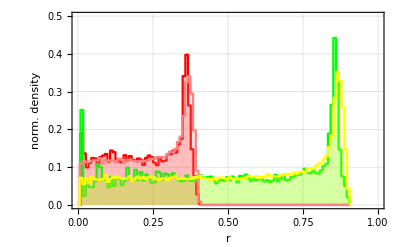
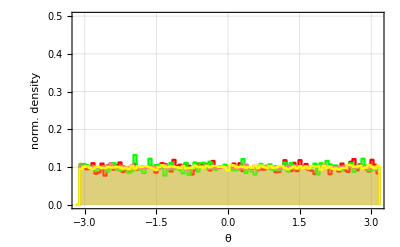
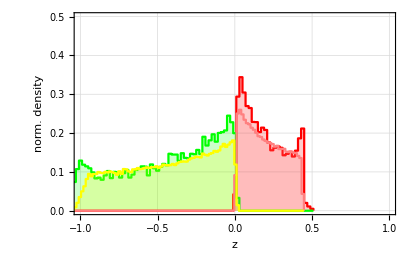

```mathematica
Table[Show[cylPlotsMCRp5Pp3[[i]], cylPlotsMegaSample[[i]]], {i,3}]
```

```mathematica
Clear[brutalMegaSample, cylPlotsMegaSample]
```

Salió parecido a lo que ya se tenía. Ahora lo interesante son aquellas gráficas que difieren y ver si, entre más brutales hay, se asemejan más.

### Poniendo más puntos a la muestra del MCS

Veamos qué pasa si la muestra MC es aún más grande

```mathematica
sampleRp5Pp3N10000 = Get["distintas_tausdeltas_Rp5Pp3/sampleMCS_n=10000_err=0.01_delta=0.01_t=0.3_rz=0.5_p=0.3.wl"][[2]];
sampleRp5Pp3N30000 = Get["distintas_tausdeltas_Rp5Pp3/sampleMCS_n=30000_err=0.01_delta=0.01_t=0.3_rz=0.5_p=0.3.wl"][[2]];
sampleRp5Pp3N50000 = Get["distintas_tausdeltas_Rp5Pp3/sampleMCS_n=50000_err=0.01_delta=0.01_t=0.3_rz=0.5_p=0.3.wl"][[2]];
```

```mathematica
mcMegaSample = Join[sampleRp5Pp3, sampleRp5Pp3N10000, sampleRp5Pp3N30000, sampleRp5Pp3N50000];
Clear[sampleRp5Pp3N10000, sampleRp5Pp3N30000, sampleRp5Pp3N50000]
```

```mathematica
cylPlotsMegaSampleMC = tripleCylindricalPlot[mcMegaSample, targets[[2]], 100, 100, 100, {Red, Green}, {0,1}, {-Pi, Pi}, {-1,1}, {0,0.5}];
```

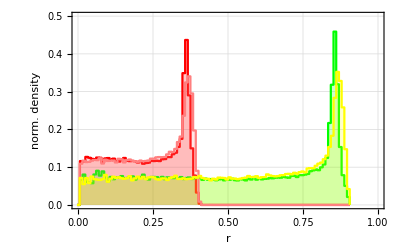
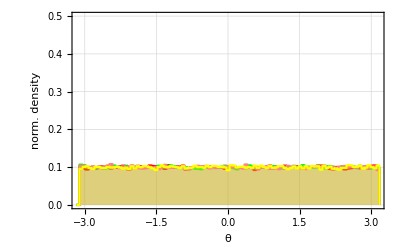
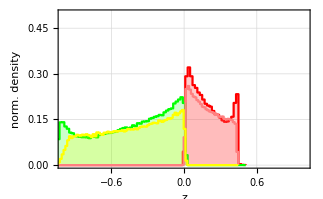

```mathematica
Table[Show[cylPlotsMegaSampleMC[[i]], cylPlotsMegaSample[[i]]], {i,3}]
```

## Midiendo ergodicidad de las preimágenes

### Target r_z = 0

```mathematica
(*orita se importan las muestras desde la sección anterior*)
```

```mathematica
(*Correspondientes muestras brutales de referencia*)
brutalRefRp0Pp3 = ketsToDensity[Get["/media/storage/ciencia/investigacion/proyecto-ss/adanerick/muestras_de_edos/pureBrutalStates/pureHaarStates_n=10000_p=0.3_rz=0.m"]][[1;;100]];
brutalRefRp0Pp5 = ketsToDensity[Get["/media/storage/ciencia/investigacion/proyecto-ss/adanerick/muestras_de_edos/pureBrutalStates/pureHaarStates_n=10000_p=0.5_rz=0.m"]][[1;;100]];
brutalRefRp0Pp8 = ketsToDensity[Get["/media/storage/ciencia/investigacion/proyecto-ss/adanerick/muestras_de_edos/pureBrutalStates/pureHaarStates_n=10000_p=0.8_rz=0.m"]][[1;;100]];
```

```mathematica
minVecRp0Pp3 = minDistancesVector[brutalRefRp0Pp3, sampleRceroPptoTres];
minVecRp0Pp5 = minDistancesVector[brutalRefRp0Pp5, sampleRceroPptoCinco];
minVecRp0Pp8 = minDistancesVector[brutalRefRp0Pp8, sampleRceroPptoOcho];
```

```mathematica
ergRp0Pp3 = ergodicityMeasure2[minVecRp0Pp3]
ergRp0Pp5 = ergodicityMeasure2[minVecRp0Pp5]
ergRp0Pp8 = ergodicityMeasure2[minVecRp0Pp8]
```

0.0785765

0.158632

0.0818361

```mathematica
(*Fidelidad ente el edo promedio del MC y el analítico*)
exactMeanStateRp0Pp3 = ρaverageTwoQubitsbasiscomp[0.3, 0.];
exactMeanStateRp0Pp5 = ρaverageTwoQubitsbasiscomp[0.5, 0.];
exactMeanStateRp0Pp8 = ρaverageTwoQubitsbasiscomp[0.2, 0.];
MCmeanStateRp0Pp3 = preimageMean[sampleRceroPptoTres];
MCmeanStateRp0Pp5 = preimageMean[sampleRceroPptoCinco];
MCmeanStateRp0Pp8 = preimageMean[sampleRceroPptoOcho];
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

```mathematica
fidelity[MCmeanStateRp0Pp3, exactMeanStateRp0Pp3]
fidelity[MCmeanStateRp0Pp5, exactMeanStateRp0Pp5]
fidelity[MCmeanStateRp0Pp8, exactMeanStateRp0Pp8]
```

0.995472

MatrixPower::mindet: Input matrix contains an indeterminate entry.

Tr[MatrixPower[{{Indeterminate,Indeterminate,Indeterminate,Indeterminate},{Indeterminate,Indeterminate,Indeterminate,Indeterminate},{Indeterminate,Indeterminate,Indeterminate,Indeterminate},{Indeterminate,Indeterminate,Indeterminate,Indeterminate}},0.5]]^2.

0.998365

### Target r_z = 0.5

```mathematica
(*Correspondientes muestras brutales de referencia*)
brutalRefRp5Pp3 = ketsToDensity[Get["/media/storage/ciencia/investigacion/proyecto-ss/adanerick/muestras_de_edos/pureBrutalStates/pureHaarStates_n=10000_p=0.3_rz=0.5.m"]][[1;;100]];
brutalRefRp5Pp5 = ketsToDensity[Get["/media/storage/ciencia/investigacion/proyecto-ss/adanerick/muestras_de_edos/pureBrutalStates/pureHaarStates_n=10000_p=0.5_rz=0.5.m"]][[1;;100]];
brutalRefRp5Pp8 = ketsToDensity[Get["/media/storage/ciencia/investigacion/proyecto-ss/adanerick/muestras_de_edos/pureBrutalStates/pureHaarStates_n=10000_p=0.8_rz=0.5.m"]][[1;;100]];
```

```mathematica
minVecRp5Pp3 = minDistancesVector[brutalRefRp5Pp3, sampleRp5Pp3];
minVecRp5Pp5 = minDistancesVector[brutalRefRp5Pp5, sampleRp5Pp5];
minVecRp5Pp8 = minDistancesVector[brutalRefRp5Pp8, sampleRp5Pp8];
```

```mathematica
ergRp5Pp3 = ergodicityMeasure2[minVecRp5Pp3]
ergRp5Pp5 = ergodicityMeasure2[minVecRp5Pp5]
ergRp5Pp8 = ergodicityMeasure2[minVecRp5Pp8]
```

0.0699621

0.0631071

0.0766136

```mathematica
(*Fidelidad ente el edo promedio del MC y el analítico*)
exactMeanStateRp5Pp3 = ρaverageTwoQubitsbasiscomp[0.3, 0.5];
exactMeanStateRp5Pp5 = ρaverageTwoQubitsbasiscomp[0.5, 0.5];
exactMeanStateRp5Pp8 = ρaverageTwoQubitsbasiscomp[0.2, 0.5];
MCmeanStateRp5Pp3 = preimageMean[sampleRp5Pp3];
MCmeanStateRp5Pp5 = preimageMean[sampleRp5Pp5];
MCmeanStateRp5Pp8 = preimageMean[sampleRp5Pp8];
```

```mathematica
fidelity[MCmeanStateRp5Pp3, exactMeanStateRp5Pp3]
fidelity[MCmeanStateRp5Pp5, exactMeanStateRp5Pp5]
fidelity[MCmeanStateRp5Pp8, exactMeanStateRp5Pp8]
```

0.999636

0.99911

0.727051

### Target r_z = 0.8

```mathematica
(*Correspondientes muestras brutales de referencia*)
brutalRefRp8Pp3 = ketsToDensity[Get["/media/storage/ciencia/investigacion/proyecto-ss/adanerick/muestras_de_edos/pureBrutalStates/pureHaarStates_n=10000_p=0.3_rz=0.8.m"]][[1;;100]];
brutalRefRp8Pp5 = ketsToDensity[Get["/media/storage/ciencia/investigacion/proyecto-ss/adanerick/muestras_de_edos/pureBrutalStates/pureHaarStates_n=10000_p=0.5_rz=0.8.m"]][[1;;100]];
brutalRefRp8Pp8 = ketsToDensity[Get["/media/storage/ciencia/investigacion/proyecto-ss/adanerick/muestras_de_edos/pureBrutalStates/pureHaarStates_n=10000_p=0.8_rz=0.8.m"]][[1;;100]];
```

```mathematica
minVecRp8Pp3 = minDistancesVector[brutalRefRp8Pp3, sampleRp8Pp3];
minVecRp8Pp5 = minDistancesVector[brutalRefRp8Pp5, sampleRp8Pp5];
minVecRp8Pp8 = minDistancesVector[brutalRefRp8Pp8, sampleRp8Pp8];
```

```mathematica
ergRp8Pp3 = ergodicityMeasure2[minVecRp8Pp3]
ergRp8Pp5 = ergodicityMeasure2[minVecRp8Pp5]
ergRp8Pp8 = ergodicityMeasure2[minVecRp8Pp8]
```

0.0486431

0.0424336

0.0565553

```mathematica
(*Fidelidad ente el edo promedio del MC y el analítico*)
exactMeanStateRp8Pp3 = ρaverageTwoQubitsbasiscomp[0.3, 0.8];
exactMeanStateRp8Pp5 = ρaverageTwoQubitsbasiscomp[0.5, 0.8];
exactMeanStateRp8Pp8 = ρaverageTwoQubitsbasiscomp[0.2, 0.8];
MCmeanStateRp8Pp3 = preimageMean[sampleRp8Pp3];
MCmeanStateRp8Pp5 = preimageMean[sampleRp8Pp5];
MCmeanStateRp8Pp8 = preimageMean[sampleRp8Pp8];
```

```mathematica
fidelity[MCmeanStateRp8Pp3, exactMeanStateRp8Pp3]
fidelity[MCmeanStateRp8Pp5, exactMeanStateRp8Pp5]
fidelity[MCmeanStateRp8Pp8, exactMeanStateRp8Pp8]
```

0.992677

0.997953

0.716066

## Errores (distancias) en función de N

```mathematica
errorsOfSample[target_, sample_, p_]:= Map[Norm[target-coarseGraining2[#, p], "Frobenius"]&, sample];
```

```mathematica
errorsR0allP = MapThread[errorsOfSample[targets[[1]], #2, #1]&, {swapPs, {sampleR0Pp3, sampleR0Pp5, sampleR0Pp8}}];
errorsRp5allP = MapThread[errorsOfSample[targets[[2]], #2, #1]&, {swapPs, {sampleRp5Pp3, sampleRp5Pp5, sampleRp5Pp8}}];
errorsRp8allP = MapThread[errorsOfSample[targets[[3]], #2, #1]&, {swapPs, {sampleRp8Pp3, sampleRp8Pp5, sampleRp8Pp8}}];
```

```mathematica
errorPlotsR0allP = Map[ListPlot[#]&, errorsR0allP];
errorPlotsRp5allP = Map[ListPlot[#]&, errorsRp5allP];
errorPlotsRp8allP = Map[ListPlot[#]&, errorsRp8allP];
```

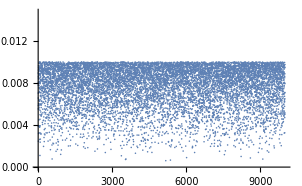
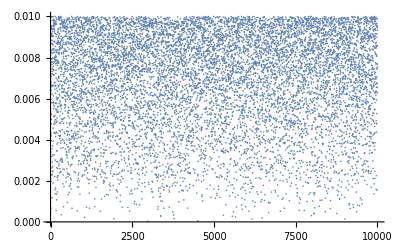
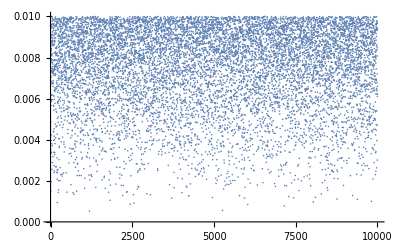
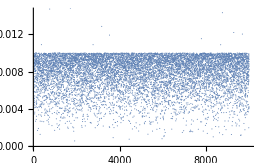
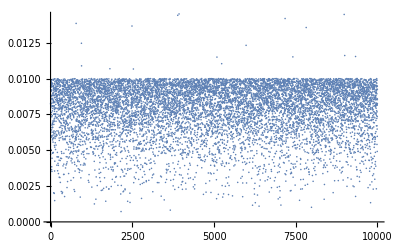
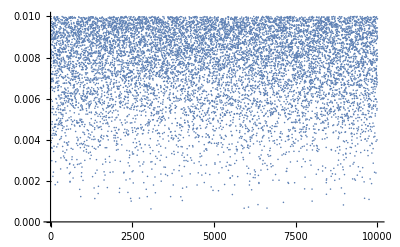
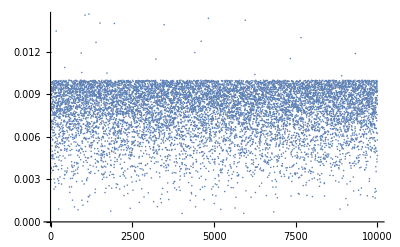
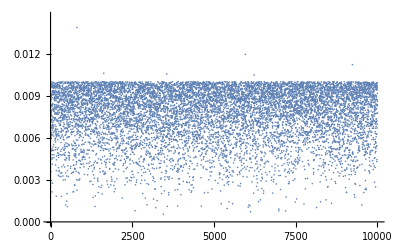
| p = 0.3 | p = 0.5 | p = 0.8
r_z = 0 | -Graphics- | -Graphics- | -Graphics-
r_z = 0.5 | -Graphics- | -Graphics- | -Graphics-
r_z = 0.8 | -Graphics- | -Graphics- | -Graphics-

```mathematica
Grid[{{, Text["p = 0.3"], Text["p = 0.5"], Text["p = 0.8"]},
	  Join[{Text["r_z = 0"]}, errorPlotsR0allP],
	  Join[{Text["r_z = 0.5"]}, errorPlotsRp5allP], 
	  Join[{Text["r_z = 0.8"]}, errorPlotsRp8allP]
}]
```

Estas gráficas de distancias y los picos de los histogramas sugieren que hay una relación entre los mencionados picos y la alta densidad de puntos en 0.01. Para ver si esto es cierto, podríamos ver cómo se relaciona la evolución que hace el estado bipartita hasta llegar a la región de interés con la evolución que harían sus correspondientes vectores r_A y r_B en la esfera de Bloch.

## Algunas pruebas con distintas deltas

### r_z =0.5, p = 0.3

Se tomaron muestras con distintas deltas, pero mismo target y probabilidad: r_z = 0.5, p =0.3.

```mathematica
taus = {0.1, 0.3, 0.5, 0.7, 0.9};
```

```mathematica
samplesδp001 = Map[Get["distintas_tausdeltas_Rp5Pp3/sampleMCS_n=10000_err=0.01_delta=0.001_t="<>ToString[#]<>"_rz=0.5_p=0.3.wl"][[2]]&, taus];
samplesδp01 =  Map[Get["distintas_tausdeltas_Rp5Pp3/sampleMCS_n=10000_err=0.01_delta=0.01_t="<>ToString[#]<>"_rz=0.5_p=0.3.wl"][[2]]&, taus];
samplesδp1 =   Map[Get["distintas_tausdeltas_Rp5Pp3/sampleMCS_n=10000_err=0.01_delta=0.1_t="<>ToString[#]<>"_rz=0.5_p=0.3.wl"][[2]]&, taus];
samplesδp02 = Map[Get["distintas_tausdeltas_Rp5Pp3/sampleMCS_n=10000_err=0.01_delta=0.02_t="<>ToString[#]<>"_rz=0.5_p=0.3.wl"][[2]]&, taus];
samplesδp03 = Map[Get["distintas_tausdeltas_Rp5Pp3/sampleMCS_n=10000_err=0.01_delta=0.03_t="<>ToString[#]<>"_rz=0.5_p=0.3.wl"][[2]]&, taus];
samplesδp04 = Map[Get["distintas_tausdeltas_Rp5Pp3/sampleMCS_n=10000_err=0.01_delta=0.04_t="<>ToString[#]<>"_rz=0.5_p=0.3.wl"][[2]]&, taus];
samplesδp05 = Map[Get["distintas_tausdeltas_Rp5Pp3/sampleMCS_n=10000_err=0.01_delta=0.05_t="<>ToString[#]<>"_rz=0.5_p=0.3.wl"][[2]]&, taus];
```

```mathematica
(*Plots od spheres*)
dotsPlotsδp001 = Map[visualizeBipartiteSystem[#]&, samplesδp001];
dotsPlotsδp01 = Map[visualizeBipartiteSystem[#]&, samplesδp01];
dotsPlotsδp1 = Map[visualizeBipartiteSystem[#]&, samplesδp1];
dotsPlotsδp02 = Map[visualizeBipartiteSystem[#]&, samplesδp02];
dotsPlotsδp03 = Map[visualizeBipartiteSystem[#]&, samplesδp03];
dotsPlotsδp04 = Map[visualizeBipartiteSystem[#]&, samplesδp04];
dotsPlotsδp05 = Map[visualizeBipartiteSystem[#]&, samplesδp05];
```

```mathematica
Clear[dotsPlotsδp001 , dotsPlotsδp01, dotsPlotsδp02, dotsPlotsδp03, dotsPlotsδp04, dotsPlotsδp05, dotsPlotsδp1]
```

```mathematica
Grid[{{, Text["τ = 0.1"], Text["τ = 0.3"], Text["τ = 0.5"], Text["τ = 0.7"], Text["τ = 0.9"]},
	  Join[{Text["δ = 0.001"]}, dotsPlotsδp001],
	  Join[{Text["δ = 0.01"]}, dotsPlotsδp01],
	  Join[{Text["δ = 0.02"]}, dotsPlotsδp02],
	  Join[{Text["δ = 0.03"]}, dotsPlotsδp03],
	  Join[{Text["δ = 0.04"]}, dotsPlotsδp04],
	  Join[{Text["δ = 0.05"]}, dotsPlotsδp05],
	  Join[{Text["δ = 0.1"]}, dotsPlotsδp1]
}]
```

| τ = 0.1 | τ = 0.3 | τ = 0.5 | τ = 0.7 | τ = 0.9
δ = 0.001 | -Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D-
δ = 0.01 | -Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D-
δ = 0.02 | -Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D-
δ = 0.03 | -Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D-
δ = 0.04 | -Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D-
δ = 0.05 | -Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D-
δ = 0.1 | -Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D-

```mathematica
(*Graficando fidelidades y errores*)

(*Datos de fidelidades*)
fidelitiesδp001 = Map[fidelity[preimageMean[#], ρaverageTwoQubitsbasiscomp[0.3, 0.5]]&, samplesδp001];
fidelitiesδp01 = Map[fidelity[preimageMean[#], ρaverageTwoQubitsbasiscomp[0.3, 0.5]]&, samplesδp01];
fidelitiesδp02 = Map[fidelity[preimageMean[#], ρaverageTwoQubitsbasiscomp[0.3, 0.5]]&, samplesδp02];
fidelitiesδp03 = Map[fidelity[preimageMean[#], ρaverageTwoQubitsbasiscomp[0.3, 0.5]]&, samplesδp03];
fidelitiesδp04 = Map[fidelity[preimageMean[#], ρaverageTwoQubitsbasiscomp[0.3, 0.5]]&, samplesδp04];
fidelitiesδp05 = Map[fidelity[preimageMean[#], ρaverageTwoQubitsbasiscomp[0.3, 0.5]]&, samplesδp05];
fidelitiesδp1  = Map[fidelity[preimageMean[#], ρaverageTwoQubitsbasiscomp[0.3, 0.5]]&, samplesδp1];
(*Datos del error*)
errorsδp001 = Map[Chop[Norm[targets[[2]]-coarseGraining2[preimageMean[#],0.3],"Frobenius"]]&, samplesδp001];
errorsδp01 = Map[Chop[Norm[targets[[2]]-coarseGraining2[preimageMean[#],0.3],"Frobenius"]]&, samplesδp01];
errorsδp02 = Map[Chop[Norm[targets[[2]]-coarseGraining2[preimageMean[#],0.3],"Frobenius"]]&, samplesδp02];
errorsδp03 = Map[Chop[Norm[targets[[2]]-coarseGraining2[preimageMean[#],0.3],"Frobenius"]]&, samplesδp03];
errorsδp04 = Map[Chop[Norm[targets[[2]]-coarseGraining2[preimageMean[#],0.3],"Frobenius"]]&, samplesδp04];
errorsδp05 = Map[Chop[Norm[targets[[2]]-coarseGraining2[preimageMean[#],0.3],"Frobenius"]]&, samplesδp05];
errorsδp1 = Map[Chop[Norm[targets[[2]]-coarseGraining2[preimageMean[#],0.3],"Frobenius"]]&, samplesδp1];
```

```mathematica
allfids = {fidelitiesδp001, fidelitiesδp01, fidelitiesδp02, fidelitiesδp03, fidelitiesδp04, fidelitiesδp05, fidelitiesδp1};
```

```mathematica
allfidsOnδ = {Map[#[[1]]&, allfids], Map[#[[2]]&, allfids], Map[#[[3]]&, allfids], Map[#[[4]]&, allfids], Map[#[[5]]&, allfids]};
```

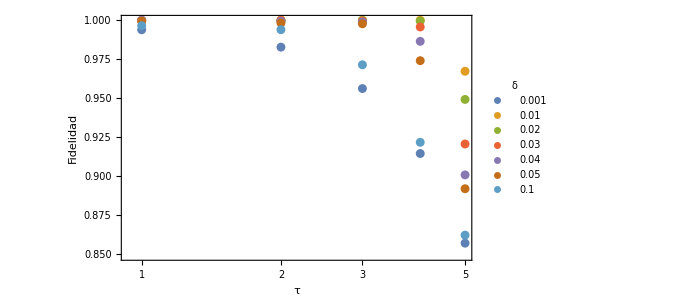
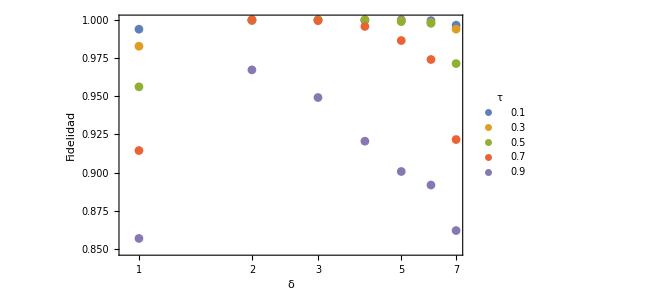
-Graphics- | -Graphics-

```mathematica
Grid[{{ListLogLinearPlot[allfids, 
			PlotTheme->"Detailed", FrameLabel->{"τ", "Fidelidad"}, PlotLegends->PointLegend[{0.001,0.01,0.02,0.03,0.04,0.05,0.1}, LegendLabel->"δ"]],
		ListLogLinearPlot[allfidsOnδ, 
			PlotTheme->"Detailed", FrameLabel->{"δ", "Fidelidad"}, PlotLegends->PointLegend[taus, LegendLabel->"τ"]]}
}]
```

### r_z=0.8 , p = 0.8

```mathematica
sampleRp8Pp8δp001 = Get["distintasDeltas_Rp8Pp8/sampleMCS_n=10000_err=0.01_delta=0.001_t=0.1_rz=0.8_p=0.8.wl"][[2]];
```

```mathematica
cylPlotsBrRp8Pp8 = tripleCylindricalPlot[brutalsRp8Pp8, targets[[3]], 100, 100, 100, {Pink, Yellow}, {0,1}, {-Pi,Pi}, {-1.5,0.3}, {0,0.6}];
cylPlotsMCRp8Pp8 = tripleCylindricalPlot[sampleRp8Pp8δp001, targets[[3]], 100, 100, 100, {Red, Green}, {0,1}, {-Pi,Pi}, {-1.5,0.3},{0,0.6}];
```

```mathematica
fidelity[preimageMean[sampleRp8Pp8δp001], preimageMean[brutalsRp8Pp8]]
fidelity[preimageMean[sampleRp8Pp8δp001], ρaverageTwoQubitsbasiscomp[0.2, 0.8]]
```

0.959475

0.695124

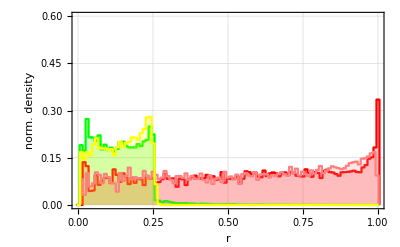
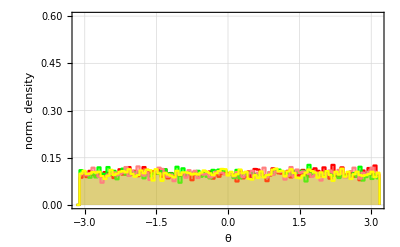
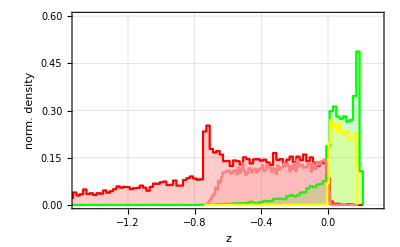
r_z = 0.8, p = 0.8 |  | 
-Graphics- | -Graphics- | -Graphics-
-Graphics3D- | -Graphics3D- |

```mathematica
Grid[{{Text["r_z = 0.8, p = 0.8"], SpanFromLeft, SpanFromLeft}, 
	  Table[Show[cylPlotsMCRp8Pp8[[i]], cylPlotsBrRp8Pp8[[i]]], {i,3}], 
	  {visualizeBipartiteSystem[sampleRp8Pp8δp001[[1;;5000]]], visualizeBipartiteSystem[brutalsRp8Pp8[[1;;2000]], {Pink,Yellow}], generalLegend}
}]
```

Con esta delta de 0.001 y tau de 0.1 (la mejor tau) salen feos los histogramas. Ya habíamos visto que con δ = 0.01 y una tau de 0.3 (un poco peor) también salen feos. Con otras deltas más grandes, el error del algoritmo es mayor según indican las gráficas de fidelidad, sea cual sea la tau que escojamos. Así, concluimos que este algoritmo no da confianza sea cual sea el valor de δ o el tamaño de la muestra. Está mejor el MH.